```mathematica
Quit[];
```

## QCD

```mathematica
(* beta function coefficients and 4-loop Lambda_QCD taken from arxiv/0908.1135 *)
```

```mathematica
β0N=(33-2Nf)/(12π);
β1N=(153-19Nf)/(24π^2);
β2N=(77139-15099Nf+325Nf^2)/(3456π^3);
β3N=(29243-6946.3Nf+405.089Nf^2+1.49931Nf^3)/(256π^4);
Mt=173.34;Mb=4.7;Mc=1.5;
ΛQCD[f_]:=Piecewise[{{.338,f==3},{.296,f==4},{.213,f==5},{.090,f==6}}]
LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]
αsNf[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
Mαs[Q_,f_]:=1+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3
αs[Q_]:=Piecewise[{{Mαs[Mc,4]Mαs[Mb,5]αsNf[1,3],Q<1},{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,3],1≤Q<Mc},{Mαs[Mb,5]αsNf[Q,4],Mc≤Q<Mb},{αsNf[Q,5],Mb≤Q<Mt},{(1/Mαs[Mt,6])αsNf[Q,6],Q≥Mt}}]
αs[2]
```

0.293951

```mathematica
αsNf[Mt,5]
```

0.107828

```mathematica
αsNf[Mt,6]
```

0.10787

```mathematica
1/(4Pi N)/.N:>5//N
```

0.0159155

```mathematica
αs[MZ]/5
```

0.0236576

```mathematica
αs[Mt]
```

0.107925

```mathematica
αsNf[Mb,5]
```

0.217151

```mathematica
αsNf[Mb,4]
```

0.215429

```mathematica
αsNf[Mc,4]
```

0.335937

```mathematica
αsNf[Mc,3]
```

0.322415

```mathematica
MZ=91.1876;
```

```mathematica
αs[MZ]
```

0.118288

```mathematica
(*LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]*)
LQs[Q_,f_]:=Log[Q^2/Λ^2]
αsNf4Loop[Q_,f_]:=(1/(β0N LQs[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2)+1/(β0N^3 LQs[Q,f]^3)(β1N^2/β0N^2(Log[LQs[Q,f]]^2-Log[LQs[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQs[Q,f]^4)(β1N^3/β0N^3(-Log[LQs[Q,f]]^3+(5/2)Log[LQs[Q,f]]^2+2Log[LQs[Q,f]]-1/2))-1/(β0N^4 LQs[Q,f]^4)(3β1N β2N Log[LQs[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf3Loop[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQs[Q,f]]^2-Log[LQs[Q,f]]-1)+β2N/β0N))/.Nf->f
αsNf2Loop[Q_,f_]:=(1/(β0N LQs[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2))/.Nf->f
αsNf1Loop[Q_,f_]:=(1/(β0N LQs[Q,f]))/.Nf->f
Mαs3Loop[Q_,f_]:=1+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3
Mαs2Loop[Q_,f_]:=1+(-.291667 )(αsNf[Q,f]/π)^2
αs4Loop[Q_]:=Piecewise[{{Mαs3Loop[Mc,4]Mαs3Loop[Mb,5]αsNf4Loop[Q,3],Q<1},{Mαs3Loop[Mc,4]Mαs3Loop[Mb,5]αsNf4Loop[Q,3],1≤Q<Mc},{Mαs3Loop[Mb,5]αsNf4Loop[Q,4],Mc≤Q<Mb},{αsNf4Loop[Q,5],Mb≤Q<Mt},{(1/Mαs3Loop[Mt,6])αsNf4Loop[Q,6],Q≥Mt}}]
αs3Loop[Q_]:=Piecewise[{{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,3],Q<1},{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,3],1≤Q<Mc},{Mαs2Loop[Mb,5]αsNf3Loop[Q,4],Mc≤Q<Mb},{αsNf3Loop[Q,5],Mb≤Q<Mt},{(1/Mαs2Loop[Mt,6])αsNf3Loop[Q,6],Q≥Mt}}]
αs2Loop[Q_]:=Piecewise[{{αsNf2Loop[Q,3],Q<1},{αsNf2Loop[Q,3],1≤Q<Mc},{αsNf2Loop[Q,4],Mc≤Q<Mb},{αsNf2Loop[Q,5],Mb≤Q<Mt},{αsNf2Loop[Q,6],Q≥Mt}}]
αs1Loop[Q_]:=Piecewise[{{αsNf1Loop[Q,3],Q<1},{αsNf1Loop[Q,3],1≤Q<Mc},{αsNf1Loop[Q,4],Mc≤Q<Mb},{αsNf1Loop[Q,5],Mb≤Q<Mt},{αsNf1Loop[Q,6],Q≥Mt}}]
```

```mathematica
Λ4LoopNf5=Λ/.FindRoot[αsNf4Loop[MZ,5]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.213

```mathematica
Λ4LoopNf6=Λ/.FindRoot[αsNf4Loop[Mt,6]-(αsNf4Loop[Mt,5]/.{Λ->Λ4LoopNf5}),{Λ,ΛQCD[6]}][[1]]
```

0.0897171

```mathematica
Λ4LoopNf4=Λ/.FindRoot[αsNf4Loop[Mb,4]-(αsNf4Loop[Mb,5]/.{Λ->Λ4LoopNf5}),{Λ,ΛQCD[4]}][[1]]
```

0.303565

```mathematica
Λ4LoopNf3=Λ/.FindRoot[αsNf4Loop[Mc,3]-(αsNf4Loop[Mc,4]/.{Λ->Λ4LoopNf4}),{Λ,ΛQCD[3]}][[1]]
```

0.378129

```mathematica
Λ3LoopNf5=Λ/.FindRoot[αsNf3Loop[MZ,5]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.217435

```mathematica
Λ3LoopNf6=Λ/.FindRoot[αsNf3Loop[Mt,6]-(αsNf3Loop[Mt,5]/.{Λ->Λ3LoopNf5}),{Λ,ΛQCD[6]}][[1]]
```

0.0910249

```mathematica
Λ3LoopNf4=Λ/.FindRoot[αsNf3Loop[Mb,4]-(αsNf3Loop[Mb,5]/.{Λ->Λ3LoopNf5}),{Λ,ΛQCD[4]}][[1]]
```

0.299152

```mathematica
Λ3LoopNf3=Λ/.FindRoot[αsNf3Loop[Mc,3]-(αsNf3Loop[Mc,4]/.{Λ->Λ3LoopNf4}),{Λ,ΛQCD[3]}][[1]]
```

0.335423

```mathematica
Λ2LoopNf5=Λ/.FindRoot[αsNf2Loop[MZ,5]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.229911

```mathematica
Λ2LoopNf6=Λ/.FindRoot[αsNf2Loop[Mt,6]-(αsNf2Loop[Mt,5]/.{Λ->Λ2LoopNf5}),{Λ,ΛQCD[6]}][[1]]
```

0.0931592

```mathematica
Λ2LoopNf4=Λ/.FindRoot[αsNf2Loop[Mb,4]-(αsNf2Loop[Mb,5]/.{Λ->Λ2LoopNf5}),{Λ,ΛQCD[4]}][[1]]
```

0.332194

```mathematica
Λ2LoopNf3=Λ/.FindRoot[αsNf2Loop[Mc,3]-(αsNf2Loop[Mc,4]/.{Λ->Λ2LoopNf4}),{Λ,ΛQCD[3]}][[1]]
```

0.386001

```mathematica
Λ1LoopNf5=Λ/.FindRoot[αsNf1Loop[MZ,5]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.0893248

```mathematica
Λ1LoopNf6=Λ/.FindRoot[αsNf1Loop[Mt,6]-(αsNf1Loop[Mt,5]/.{Λ->Λ1LoopNf5}),{Λ,ΛQCD[6]}][[1]]
```

0.0434346

```mathematica
Λ1LoopNf4=Λ/.FindRoot[αsNf1Loop[Mb,4]-(αsNf1Loop[Mb,5]/.{Λ->Λ1LoopNf5}),{Λ,ΛQCD[4]}][[1]]
```

0.122648

```mathematica
Λ1LoopNf3=Λ/.FindRoot[αsNf1Loop[Mc,3]-(αsNf1Loop[Mc,4]/.{Λ->Λ1LoopNf4}),{Λ,ΛQCD[3]}][[1]]
```

0.147643

```mathematica
αsNf1Loop[Mb,5]/.{Λ->Λ1LoopNf5}
```

0.206797

```mathematica
αsNf1Loop[Mb,4]/.{Λ->Λ1LoopNf4}
```

0.206797

```mathematica
αsNf1Loop[Mc,4]/.{Λ->Λ1LoopNf4}
```

0.301123

```mathematica
αsNf1Loop[Mc,3]/.{Λ->Λ1LoopNf3}
```

0.301123

```mathematica
(* don't freeze out evolution for Q < 1 GeV *)
```

```mathematica
β0N=(33-2Nf)/(12π);
β1N=(153-19Nf)/(24π^2);
β2N=(77139-15099Nf+325Nf^2)/(3456π^3);
β3N=(29243-6946.3Nf+405.089Nf^2+1.49931Nf^3)/(256π^4);
Mt=173.34;Mb=4.7;Mc=1.5;
ΛQCD[f_]:=Piecewise[{{Λ4LoopNf3,f==3},{Λ4LoopNf4,f==4},{Λ4LoopNf5,f==5},{Λ4LoopNf6,f==6}}]
ΛQCD3Loop[f_]:=Piecewise[{{Λ3LoopNf3,f==3},{Λ3LoopNf4,f==4},{Λ3LoopNf5,f==5},{Λ3LoopNf6,f==6}}]
ΛQCD2Loop[f_]:=Piecewise[{{Λ2LoopNf3,f==3},{Λ2LoopNf4,f==4},{Λ2LoopNf5,f==5},{Λ2LoopNf6,f==6}}]
ΛQCD1Loop[f_]:=Piecewise[{{Λ1LoopNf3,f==3},{Λ1LoopNf4,f==4},{Λ1LoopNf5,f==5},{Λ1LoopNf6,f==6}}]
LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]
LQ3Loop[Q_,f_]:=Log[Q^2/ΛQCD3Loop[f]^2]
LQ2Loop[Q_,f_]:=Log[Q^2/ΛQCD2Loop[f]^2]
LQ1Loop[Q_,f_]:=Log[Q^2/ΛQCD1Loop[f]^2]
αsNf[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf4Loop[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf3Loop[Q_,f_]:=(1/(β0N LQ3Loop[Q,f])-β1N Log[LQ3Loop[Q,f]]/(β0N^3LQ3Loop[Q,f]^2)+1/(β0N^3 LQ3Loop[Q,f]^3)(β1N^2/β0N^2(Log[LQ3Loop[Q,f]]^2-Log[LQ3Loop[Q,f]]-1)+β2N/β0N))/.Nf->f
αsNf2Loop[Q_,f_]:=(1/(β0N LQ2Loop[Q,f])-β1N Log[LQ2Loop[Q,f]]/(β0N^3LQ[Q,f]^2))/.Nf->f
αsNf1Loop[Q_,f_]:=(1/(β0N LQ1Loop[Q,f]))/.Nf->f
Mαs[Q_,f_]:=1+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3
Mαs2Loop[Q_,f_]:=1+(-.291667 )(αsNf3Loop[Q,f]/π)^2
αs[Q_]:=Piecewise[{{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,3],Q<1},{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,3],1≤Q<Mc},{Mαs[Mb,5]αsNf[Q,4],Mc≤Q<Mb},{αsNf[Q,5],Mb≤Q<Mt},{(1/Mαs[Mt,6])αsNf[Q,6],Q≥Mt}}]
αs3Loop[Q_]:=Piecewise[{{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,3],Q<1},{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,3],1≤Q<Mc},{Mαs2Loop[Mb,5]αsNf3Loop[Q,4],Mc≤Q<Mb},{αsNf3Loop[Q,5],Mb≤Q<Mt},{(1/Mαs2Loop[Mt,6])αsNf3Loop[Q,6],Q≥Mt}}]
αs2Loop[Q_]:=Piecewise[{{αsNf2Loop[Q,3],Q<1},{αsNf2Loop[Q,3],1≤Q<Mc},{αsNf2Loop[Q,4],Mc≤Q<Mb},{αsNf2Loop[Q,5],Mb≤Q<Mt},{αsNf2Loop[Q,6],Q≥Mt}}]
αs1Loop[Q_]:=Piecewise[{{αsNf1Loop[Q,3],Q<1},{αsNf1Loop[Q,3],1≤Q<Mc},{αsNf1Loop[Q,4],Mc≤Q<Mb},{αsNf1Loop[Q,5],Mb≤Q<Mt},{αsNf1Loop[Q,6],Q≥Mt}}]
αs[2]
αs3Loop[2]
αs2Loop[2]
αs1Loop[2]
```

0.297172

0.304349

0.319784

0.270092

```mathematica
μoΛTab=1/{.95,.75,.5,.25,.05,.01,.001}
```

{1.05263,1.33333,2.,4.,20.,100.,1000.}

```mathematica
Mc/ΛQCD3Loop[4]
Mc/ΛQCD2Loop[4]
Mc/ΛQCD1Loop[4]
```

5.01418

4.51544

12.2301

```mathematica
Mb/ΛQCD3Loop[5]
Mb/ΛQCD2Loop[5]
Mb/ΛQCD1Loop[5]
```

21.6157

20.4427

52.617

```mathematica
Mt/ΛQCD3Loop[6]
Mt/ΛQCD2Loop[6]
Mt/ΛQCD1Loop[6]
```

1904.31

1860.69

3990.83

```mathematica
nfTab={3,3,3,3,4,5,5};
```

```mathematica
ΛQCDTab=Table[ΛQCD[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD3LoopTab=Table[ΛQCD3Loop[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD2LoopTab=Table[ΛQCD2Loop[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD1LoopTab=Table[ΛQCD1Loop[nfTab[[n]]],{n,Length[nfTab]}]
```

{0.378129,0.378129,0.378129,0.378129,0.303565,0.213,0.213}

{0.335423,0.335423,0.335423,0.335423,0.299152,0.217435,0.217435}

{0.386001,0.386001,0.386001,0.386001,0.332194,0.229911,0.229911}

{0.147643,0.147643,0.147643,0.147643,0.122648,0.0893248,0.0893248}

```mathematica
μGeVTab=μoΛTab ΛQCDTab
```

{0.398031,0.504173,0.756259,1.51252,6.07131,21.3,213.}

```mathematica
μGeV3LoopTab=μoΛTab ΛQCD3LoopTab
```

{0.353077,0.447231,0.670847,1.34169,5.98303,21.7435,217.435}

```mathematica
μGeV2LoopTab=μoΛTab ΛQCD2LoopTab
```

{0.406317,0.514668,0.772002,1.544,6.64387,22.9911,229.911}

```mathematica
μGeV1LoopTab=μoΛTab ΛQCD1LoopTab
```

{0.155414,0.196857,0.295286,0.590571,2.45297,8.93248,89.3248}

```mathematica
Table[αs[μGeVTab[[n]]],{n,Length[nfTab]}]
```

{175565.,8.76424,0.344226,0.337729,0.202298,0.151919,0.105198}

```mathematica
Table[αs3Loop[μGeV3LoopTab[[n]]],{n,Length[nfTab]}]
```

{6578.04,10.0428,0.878876,0.373108,0.204763,0.152134,0.105092}

```mathematica
Table[αs2Loop[μGeV2LoopTab[[n]]],{n,Length[nfTab]}]
```

{135.103,4.03082,0.830355,0.372494,0.200221,0.150653,0.104287}

```mathematica
Table[αs1Loop[μGeV1LoopTab[[n]]],{n,Length[nfTab]}]
```

{13.6106,2.42675,1.00719,0.503596,0.251685,0.177962,0.118641}

```mathematica
αs[1]
```

0.395109

```mathematica
αs3Loop[1]
```

0.47641

```mathematica
αs2Loop[1]
```

0.545637

```mathematica
αs1Loop[1]
```

0.364949

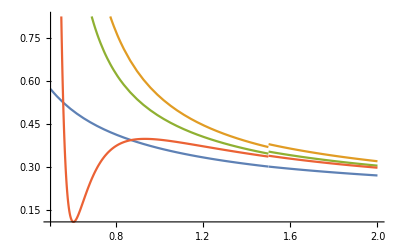

```mathematica
Plot[{αs1Loop[μ],αs2Loop[μ],αs3Loop[μ],αs[μ]},{μ,.5,2}]
```

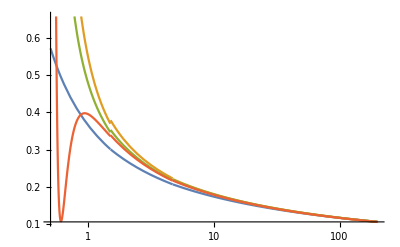

```mathematica
LogLinearPlot[{αs1Loop[μ],αs2Loop[μ],αs3Loop[μ],αs[μ]},{μ,.5,200}]
```

## dQCD

```mathematica
CF=(N^2-1)/(2N);
CA=N;
dFA=N(N^2+6)/48;
dFF=(N^4-6N^2+18)/(96N^2);
dAA=N^2(N^2+36)/24;
beta0=(1/(4Pi))*(11/3*CA-2/3*Nf);
beta1=(1/(4Pi))^2*(34/3*CA^2-10/3*CA Nf-2CF Nf);
beta2=(1/(4Pi))^3*(2857/54*CA^3-1415/27*CA^2*Nf/2+158/27*CA*Nf^2/4+44/9*CF Nf^2/4-205/9*CF*CA*Nf/2+CF^2 Nf);
beta3=(1/(4Pi))^4*(CA CF Nf^2/4(17152/243+448/9Zeta[3])+CA CF^2 Nf/2(-4204/27+352/9Zeta[3])+424/243CA Nf^3/8 +1232/243CF Nf^3/8 + CA^2CF Nf/2(7073/243-656/9*Zeta[3])+CA^2*Nf^2/4(7930/81+224/9*Zeta[3])+CA^3*Nf/2(-39143/81+136/3*Zeta[3])+CA^4*(150653/486-44/9*Zeta[3])+CF^2*Nf^2/4(1352/27-704/9*Zeta[3])+46*CF^3*Nf/2+Nf*dFA*(512/9-1664/3*Zeta[3])+Nf^2*dFF*(-704/9+512/3*Zeta[3])+dAA(-80/9+704/3*Zeta[3]));
```

### Nd=3

#### Running

```mathematica
(* beta function coefficients and 4-loop Lambda_QCD taken from arxiv/0908.1135 *)
```

```mathematica
β0N=beta0/.N:>3;
β1N=beta1/.N:>3;
β2N=beta2/.N:>3;
β3N=beta3/.N:>3;
Mt=173.34;Mb=4.7;Mc=1.5;
ΛQCD[f_]:=Piecewise[{{.2,f==0},{.338,f==3},{.296,f==4},{.213,f==5},{.090,f==6}}]
LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]
αsNf[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
Mαs[Q_,f_]:=1(*+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3*)
αs[Q_]:=Piecewise[{{Mαs[Mc,4]Mαs[Mb,5]αsNf[1,0],Q<1},{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,0],1≤Q<Mc},{Mαs[Mb,5]αsNf[Q,0],Mc≤Q<Mb},{αsNf[Q,0],Mb≤Q<Mt},{(1/Mαs[Mt,6])αsNf[Q,0],Q≥Mt}}]*3/N /.N:>3
αs[3]
```

0.16074

```mathematica
MZ=91.1876;
```

```mathematica
αs[MZ]
```

0.07884

```mathematica
(*LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]*)
LQs[Q_,f_]:=Log[Q^2/Λ^2]
αsNf4Loop[Q_,f_]:=(1/(β0N LQs[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2)+1/(β0N^3 LQs[Q,f]^3)(β1N^2/β0N^2(Log[LQs[Q,f]]^2-Log[LQs[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQs[Q,f]^4)(β1N^3/β0N^3(-Log[LQs[Q,f]]^3+(5/2)Log[LQs[Q,f]]^2+2Log[LQs[Q,f]]-1/2))-1/(β0N^4 LQs[Q,f]^4)(3β1N β2N Log[LQs[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf3Loop[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQs[Q,f]]^2-Log[LQs[Q,f]]-1)+β2N/β0N))/.Nf->f
αsNf2Loop[Q_,f_]:=(1/(β0N LQs[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2))/.Nf->f
αsNf1Loop[Q_,f_]:=(1/(β0N LQs[Q,f]))/.Nf->f
Mαs3Loop[Q_,f_]:=1(*+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3*)
Mαs2Loop[Q_,f_]:=1(*+(-.291667 )(αsNf[Q,f]/π)^2*)
αs4Loop[Q_]:=Piecewise[{{Mαs3Loop[Mc,4]Mαs3Loop[Mb,5]αsNf4Loop[Q,0],Q<1},{Mαs3Loop[Mc,4]Mαs3Loop[Mb,5]αsNf4Loop[Q,0],1≤Q<Mc},{Mαs3Loop[Mb,5]αsNf4Loop[Q,0],Mc≤Q<Mb},{αsNf4Loop[Q,0],Mb≤Q<Mt},{(1/Mαs3Loop[Mt,6])αsNf4Loop[Q,0],Q≥Mt}}]
αs3Loop[Q_]:=Piecewise[{{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,0],Q<1},{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,0],1≤Q<Mc},{Mαs2Loop[Mb,5]αsNf3Loop[Q,0],Mc≤Q<Mb},{αsNf3Loop[Q,0],Mb≤Q<Mt},{(1/Mαs2Loop[Mt,6])αsNf3Loop[Q,0],Q≥Mt}}]
αs2Loop[Q_]:=Piecewise[{{αsNf2Loop[Q,0],Q<1},{αsNf2Loop[Q,0],1≤Q<Mc},{αsNf2Loop[Q,0],Mc≤Q<Mb},{αsNf2Loop[Q,0],Mb≤Q<Mt},{αsNf2Loop[Q,0],Q≥Mt}}]
αs1Loop[Q_]:=Piecewise[{{αsNf1Loop[Q,0],Q<1},{αsNf1Loop[Q,0],1≤Q<Mc},{αsNf1Loop[Q,0],Mc≤Q<Mb},{αsNf1Loop[Q,0],Mb≤Q<Mt},{αsNf1Loop[Q,0],Q≥Mt}}]
```

```mathematica
Λ4LoopNf0=Λ/.FindRoot[αsNf4Loop[MZ,0]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.2

```mathematica
Λ3LoopNf0=Λ/.FindRoot[αsNf3Loop[MZ,0]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.211767

```mathematica
Λ2LoopNf0=Λ/.FindRoot[αsNf2Loop[MZ,0]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.231173

```mathematica
Λ1LoopNf0=Λ/.FindRoot[αsNf1Loop[MZ,0]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.0650813

```mathematica
(* don't freeze out evolution for Q < 1 GeV *)
```

```mathematica
β0N=beta0/.N:>3;
β1N=beta1/.N:>3;
β2N=beta2/.N:>3;
β3N=beta3/.N:>3;
Mt=173.34;Mb=4.7;Mc=1.5;
ΛQCD[f_]:=Λ4LoopNf0
ΛQCD3Loop[f_]:=Λ3LoopNf0
ΛQCD2Loop[f_]:=Λ2LoopNf0
ΛQCD1Loop[f_]:=Λ1LoopNf0
LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]
LQ3Loop[Q_,f_]:=Log[Q^2/ΛQCD3Loop[f]^2]
LQ2Loop[Q_,f_]:=Log[Q^2/ΛQCD2Loop[f]^2]
LQ1Loop[Q_,f_]:=Log[Q^2/ΛQCD1Loop[f]^2]
αsNf[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf4Loop[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf3Loop[Q_,f_]:=(1/(β0N LQ3Loop[Q,f])-β1N Log[LQ3Loop[Q,f]]/(β0N^3LQ3Loop[Q,f]^2)+1/(β0N^3 LQ3Loop[Q,f]^3)(β1N^2/β0N^2(Log[LQ3Loop[Q,f]]^2-Log[LQ3Loop[Q,f]]-1)+β2N/β0N))/.Nf->f
αsNf2Loop[Q_,f_]:=(1/(β0N LQ2Loop[Q,f])-β1N Log[LQ2Loop[Q,f]]/(β0N^3LQ[Q,f]^2))/.Nf->f
αsNf1Loop[Q_,f_]:=(1/(β0N LQ1Loop[Q,f]))/.Nf->f
Mαs[Q_,f_]:=1(*+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3*)
Mαs2Loop[Q_,f_]:=1(*+(-.291667 )(αsNf3Loop[Q,f]/π)^2*)
αs[Q_]:=Piecewise[{{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,0],Q<1},{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,0],1≤Q<Mc},{Mαs[Mb,5]αsNf[Q,0],Mc≤Q<Mb},{αsNf[Q,0],Mb≤Q<Mt},{(1/Mαs[Mt,6])αsNf[Q,0],Q≥Mt}}]
αs3Loop[Q_]:=Piecewise[{{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,0],Q<1},{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,0],1≤Q<Mc},{Mαs2Loop[Mb,5]αsNf3Loop[Q,0],Mc≤Q<Mb},{αsNf3Loop[Q,0],Mb≤Q<Mt},{(1/Mαs2Loop[Mt,6])αsNf3Loop[Q,0],Q≥Mt}}]
αs2Loop[Q_]:=Piecewise[{{αsNf2Loop[Q,0],Q<1},{αsNf2Loop[Q,0],1≤Q<Mc},{αsNf2Loop[Q,0],Mc≤Q<Mb},{αsNf2Loop[Q,0],Mb≤Q<Mt},{αsNf2Loop[Q,0],Q≥Mt}}]
αs1Loop[Q_]:=Piecewise[{{αsNf1Loop[Q,0],Q<1},{αsNf1Loop[Q,0],1≤Q<Mc},{αsNf1Loop[Q,0],Mc≤Q<Mb},{αsNf1Loop[Q,0],Mb≤Q<Mt},{αsNf1Loop[Q,0],Q≥Mt}}]
αs[2]
αs3Loop[2]
αs2Loop[2]
αs1Loop[2]
```

0.183929

0.193995

0.198324

0.16676

```mathematica
μoΛTab=1/{.95,.75,.5,.25,.05,.01,.001}
```

{1.05263,1.33333,2.,4.,20.,100.,1000.}

```mathematica
Mc/ΛQCD3Loop[4]
Mc/ΛQCD2Loop[4]
Mc/ΛQCD1Loop[4]
```

7.08325

6.48864

23.0481

```mathematica
Mb/ΛQCD3Loop[5]
Mb/ΛQCD2Loop[5]
Mb/ΛQCD1Loop[5]
```

22.1942

20.3311

72.2174

```mathematica
Mt/ΛQCD3Loop[6]
Mt/ΛQCD2Loop[6]
Mt/ΛQCD1Loop[6]
```

818.54

749.827

2663.44

```mathematica
nfTab={0,0,0,0,0,0,0};
```

```mathematica
ΛQCDTab=Table[ΛQCD[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD3LoopTab=Table[ΛQCD3Loop[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD2LoopTab=Table[ΛQCD2Loop[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD1LoopTab=Table[ΛQCD1Loop[nfTab[[n]]],{n,Length[nfTab]}]
```

{0.2,0.2,0.2,0.2,0.2,0.2,0.2}

{0.211767,0.211767,0.211767,0.211767,0.211767,0.211767,0.211767}

{0.231173,0.231173,0.231173,0.231173,0.231173,0.231173,0.231173}

{0.0650813,0.0650813,0.0650813,0.0650813,0.0650813,0.0650813,0.0650813}

```mathematica
μGeVTab=μoΛTab ΛQCDTab
```

{0.210526,0.266667,0.4,0.8,4.,20.,200.}

```mathematica
μGeV3LoopTab=μoΛTab ΛQCD3LoopTab
```

{0.222913,0.282356,0.423534,0.847069,4.23534,21.1767,211.767}

```mathematica
μGeV2LoopTab=μoΛTab ΛQCD2LoopTab
```

{0.24334,0.308231,0.462347,0.924693,4.62347,23.1173,231.173}

```mathematica
μGeV1LoopTab=μoΛTab ΛQCD1LoopTab
```

{0.0685066,0.0867751,0.130163,0.260325,1.30163,6.50813,65.0813}

```mathematica
Table[αs[μGeVTab[[n]]],{n,Length[nfTab]}]
```

{181472.,10.4543,0.237118,0.267327,0.14756,0.101565,0.0707307}

```mathematica
Table[αs3Loop[μGeV3LoopTab[[n]]],{n,Length[nfTab]}]
```

{6214.1,9.42661,0.748873,0.304487,0.149909,0.102174,0.0709126}

```mathematica
Table[αs2Loop[μGeV2LoopTab[[n]]],{n,Length[nfTab]}]
```

{25.3853,2.69684,0.712084,0.307309,0.14697,0.100342,0.0699798}

```mathematica
Table[αs1Loop[μGeV1LoopTab[[n]]],{n,Length[nfTab]}]
```

{11.1359,1.98552,0.824065,0.412033,0.190671,0.124034,0.0826895}

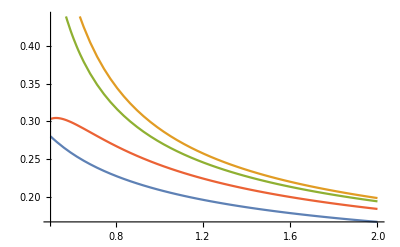

```mathematica
Plot[{αs1Loop[μ],αs2Loop[μ],αs3Loop[μ],αs[μ]},{μ,.5,2}]
```

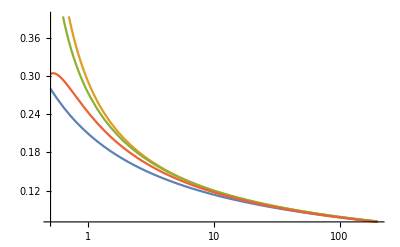

```mathematica
LogLinearPlot[{αs1Loop[μ],αs2Loop[μ],αs3Loop[μ],αs[μ]},{μ,.5,200}]
```

#### alpha tables

```mathematica
μoΛTab=1/{.19,.15,.11,.07,.046,.044,.02,.005,.001,.0006,.0005,.0003,.0001,.00003,.00001}
```

{5.26316,6.66667,9.09091,14.2857,21.7391,22.7273,50.,200.,1000.,1666.67,2000.,3333.33,10000.,33333.3,100000.}

```mathematica
nfTab=Table[0,{n,Length[μoΛTab]}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Length[nfTab]
```

15

```mathematica
ΛQCDTab=Table[ΛQCD[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD3LoopTab=Table[ΛQCD3Loop[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD2LoopTab=Table[ΛQCD2Loop[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD1LoopTab=Table[ΛQCD1Loop[nfTab[[n]]],{n,Length[nfTab]}]
```

{0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2}

{0.211767,0.211767,0.211767,0.211767,0.211767,0.211767,0.211767,0.211767,0.211767,0.211767,0.211767,0.211767,0.211767,0.211767,0.211767}

{0.231173,0.231173,0.231173,0.231173,0.231173,0.231173,0.231173,0.231173,0.231173,0.231173,0.231173,0.231173,0.231173,0.231173,0.231173}

{0.0650813,0.0650813,0.0650813,0.0650813,0.0650813,0.0650813,0.0650813,0.0650813,0.0650813,0.0650813,0.0650813,0.0650813,0.0650813,0.0650813,0.0650813}

```mathematica
μGeVTab=μoΛTab ΛQCDTab
```

{1.05263,1.33333,1.81818,2.85714,4.34783,4.54545,10.,40.,200.,333.333,400.,666.667,2000.,6666.67,20000.}

```mathematica
μGeV3LoopTab=μoΛTab ΛQCD3LoopTab
```

{1.11456,1.41178,1.92516,3.02525,4.60364,4.81289,10.5884,42.3534,211.767,352.945,423.534,705.891,2117.67,7058.91,21176.7}

```mathematica
μGeV2LoopTab=μoΛTab ΛQCD2LoopTab
```

{1.2167,1.54116,2.10158,3.30248,5.02551,5.25394,11.5587,46.2347,231.173,385.289,462.347,770.578,2311.73,7705.78,23117.3}

```mathematica
μGeV1LoopTab=μoΛTab ΛQCD1LoopTab
```

{0.342533,0.433875,0.591648,0.929733,1.41481,1.47912,3.25406,13.0163,65.0813,108.469,130.163,216.938,650.813,2169.38,6508.13}

```mathematica
α4Tab=Table[{μoΛTab[[n]],αs[μGeVTab[[n]]]},{n,Length[nfTab]}]
```

(5.26316 | 0.237056
6.66667 | 0.214629
9.09091 | 0.190369
14.2857 | 0.163216
21.7391 | 0.144141
22.7273 | 0.142384
50. | 0.117195
200. | 0.0897027
1000. | 0.0707307
1666.67 | 0.0663143
2000. | 0.0648716
3333.33 | 0.0611515
10000. | 0.0544613
33333.3 | 0.048655
100000. | 0.0443562)

```mathematica
α3Tab=Table[{μoΛTab[[n]],αs3Loop[μGeV3LoopTab[[n]]]},{n,Length[nfTab]}]
```

(5.26316 | 0.255794
6.66667 | 0.22608
9.09091 | 0.197013
14.2857 | 0.166707
21.7391 | 0.146289
22.7273 | 0.144434
50. | 0.1182
200. | 0.0901024
1000. | 0.0709126
1666.67 | 0.0664615
2000. | 0.0650086
3333.33 | 0.0612645
10000. | 0.0545388
33333.3 | 0.0487088
100000. | 0.0443961)

```mathematica
α2Tab=Table[{μoΛTab[[n]],αs2Loop[μGeV2LoopTab[[n]]]},{n,Length[nfTab]}]
```

(5.26316 | 0.255297
6.66667 | 0.224093
9.09091 | 0.194163
14.2857 | 0.163627
21.7391 | 0.143402
22.7273 | 0.141577
50. | 0.115918
200. | 0.0886262
1000. | 0.0699798
1666.67 | 0.0656446
2000. | 0.0642284
3333.33 | 0.0605757
10000. | 0.0540026
33333.3 | 0.0482911
100000. | 0.0440572)

```mathematica
α1Tab=Table[{μoΛTab[[n]],αs1Loop[μGeV1LoopTab[[n]]]},{n,Length[nfTab]}]
```

(5.26316 | 0.343944
6.66667 | 0.301087
9.09091 | 0.25878
14.2857 | 0.214796
21.7391 | 0.185507
22.7273 | 0.182868
50. | 0.146011
200. | 0.107808
1000. | 0.0826895
1666.67 | 0.0769957
2000. | 0.0751488
3333.33 | 0.0704164
10000. | 0.0620171
33333.3 | 0.0548475
100000. | 0.0496137)

```mathematica
α4Tab[[All,2]]
```

{0.237056,0.214629,0.190369,0.163216,0.144141,0.142384,0.117195,0.0897027,0.0707307,0.0663143,0.0648716,0.0611515,0.0544613,0.048655,0.0443562}

```mathematica
<<MaTeX`
```

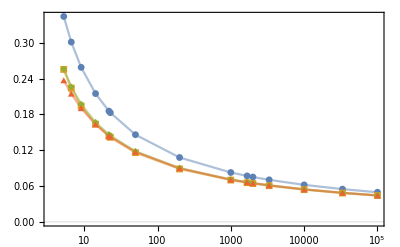

```mathematica
Show[ListLogLinearPlot[{α1Tab,α2Tab,α3Tab,α4Tab},PlotStyle->{Opacity[.5]},Joined->True],ListLogLinearPlot[{α1Tab,α2Tab,α3Tab,α4Tab},PlotMarkers->{Automatic, Small}],BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],Frame->True,Axes->False,GridLines->{{0},{0}},FrameLabel->{MaTeX["\\mu/\\Lambda_{QCD}",Magnification->1.2],MaTeX["\\alpha_s(\\mu/\\Lambda_{QCD})",Magnification->1.2]}]
```

### Nd=4

#### Running

```mathematica
(* beta function coefficients and 4-loop Lambda_QCD taken from arxiv/0908.1135 *)
```

```mathematica
β0N=beta0/.N:>4;
β1N=beta1/.N:>4;
β2N=beta2/.N:>4;
β3N=beta3/.N:>4;
Mt=173.34;Mb=4.7;Mc=1.5;
ΛQCD[f_]:=Piecewise[{{.2,f==0},{.338,f==3},{.296,f==4},{.213,f==5},{.090,f==6}}]
LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]
αsNf[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
Mαs[Q_,f_]:=1(*+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3*)
αs[Q_]:=Piecewise[{{Mαs[Mc,4]Mαs[Mb,5]αsNf[1,0],Q<1},{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,0],1≤Q<Mc},{Mαs[Mb,5]αsNf[Q,0],Mc≤Q<Mb},{αsNf[Q,0],Mb≤Q<Mt},{(1/Mαs[Mt,6])αsNf[Q,0],Q≥Mt}}]*3/N /.N:>4
αs[3]
```

0.0904573

```mathematica
MZ=91.1876;
```

```mathematica
αs[MZ]
```

0.0443491

```mathematica
(*LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]*)
LQs[Q_,f_]:=Log[Q^2/Λ^2]
αsNf4Loop[Q_,f_]:=(1/(β0N LQs[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2)+1/(β0N^3 LQs[Q,f]^3)(β1N^2/β0N^2(Log[LQs[Q,f]]^2-Log[LQs[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQs[Q,f]^4)(β1N^3/β0N^3(-Log[LQs[Q,f]]^3+(5/2)Log[LQs[Q,f]]^2+2Log[LQs[Q,f]]-1/2))-1/(β0N^4 LQs[Q,f]^4)(3β1N β2N Log[LQs[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf3Loop[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQs[Q,f]]^2-Log[LQs[Q,f]]-1)+β2N/β0N))/.Nf->f
αsNf2Loop[Q_,f_]:=(1/(β0N LQs[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2))/.Nf->f
αsNf1Loop[Q_,f_]:=(1/(β0N LQs[Q,f]))/.Nf->f
Mαs3Loop[Q_,f_]:=1(*+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3*)
Mαs2Loop[Q_,f_]:=1(*+(-.291667 )(αsNf[Q,f]/π)^2*)
αs4Loop[Q_]:=Piecewise[{{Mαs3Loop[Mc,4]Mαs3Loop[Mb,5]αsNf4Loop[Q,0],Q<1},{Mαs3Loop[Mc,4]Mαs3Loop[Mb,5]αsNf4Loop[Q,0],1≤Q<Mc},{Mαs3Loop[Mb,5]αsNf4Loop[Q,0],Mc≤Q<Mb},{αsNf4Loop[Q,0],Mb≤Q<Mt},{(1/Mαs3Loop[Mt,6])αsNf4Loop[Q,0],Q≥Mt}}]
αs3Loop[Q_]:=Piecewise[{{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,0],Q<1},{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,0],1≤Q<Mc},{Mαs2Loop[Mb,5]αsNf3Loop[Q,0],Mc≤Q<Mb},{αsNf3Loop[Q,0],Mb≤Q<Mt},{(1/Mαs2Loop[Mt,6])αsNf3Loop[Q,0],Q≥Mt}}]
αs2Loop[Q_]:=Piecewise[{{αsNf2Loop[Q,0],Q<1},{αsNf2Loop[Q,0],1≤Q<Mc},{αsNf2Loop[Q,0],Mc≤Q<Mb},{αsNf2Loop[Q,0],Mb≤Q<Mt},{αsNf2Loop[Q,0],Q≥Mt}}]
αs1Loop[Q_]:=Piecewise[{{αsNf1Loop[Q,0],Q<1},{αsNf1Loop[Q,0],1≤Q<Mc},{αsNf1Loop[Q,0],Mc≤Q<Mb},{αsNf1Loop[Q,0],Mb≤Q<Mt},{αsNf1Loop[Q,0],Q≥Mt}}]
```

```mathematica
Λ4LoopNf0=Λ/.FindRoot[αsNf4Loop[MZ,0]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

-0.0201654

```mathematica
Λ3LoopNf0=Λ/.FindRoot[αsNf3Loop[MZ,0]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

2.26665

```mathematica
Λ2LoopNf0=Λ/.FindRoot[αsNf2Loop[MZ,0]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.0231337

```mathematica
Λ1LoopNf0=Λ/.FindRoot[αsNf1Loop[MZ,0]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

-0.00581807

```mathematica
(* don't freeze out evolution for Q < 1 GeV *)
```

```mathematica
β0N=beta0/.N:>4;
β1N=beta1/.N:>4;
β2N=beta2/.N:>4;
β3N=beta3/.N:>4;
Mt=173.34;Mb=4.7;Mc=1.5;
ΛQCD[f_]:=Λ4LoopNf0
ΛQCD3Loop[f_]:=Λ3LoopNf0
ΛQCD2Loop[f_]:=Λ2LoopNf0
ΛQCD1Loop[f_]:=Λ1LoopNf0
LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]
LQ3Loop[Q_,f_]:=Log[Q^2/ΛQCD3Loop[f]^2]
LQ2Loop[Q_,f_]:=Log[Q^2/ΛQCD2Loop[f]^2]
LQ1Loop[Q_,f_]:=Log[Q^2/ΛQCD1Loop[f]^2]
αsNf[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf4Loop[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf3Loop[Q_,f_]:=(1/(β0N LQ3Loop[Q,f])-β1N Log[LQ3Loop[Q,f]]/(β0N^3LQ3Loop[Q,f]^2)+1/(β0N^3 LQ3Loop[Q,f]^3)(β1N^2/β0N^2(Log[LQ3Loop[Q,f]]^2-Log[LQ3Loop[Q,f]]-1)+β2N/β0N))/.Nf->f
αsNf2Loop[Q_,f_]:=(1/(β0N LQ2Loop[Q,f])-β1N Log[LQ2Loop[Q,f]]/(β0N^3LQ[Q,f]^2))/.Nf->f
αsNf1Loop[Q_,f_]:=(1/(β0N LQ1Loop[Q,f]))/.Nf->f
Mαs[Q_,f_]:=1(*+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3*)
Mαs2Loop[Q_,f_]:=1(*+(-.291667 )(αsNf3Loop[Q,f]/π)^2*)
αs[Q_]:=Piecewise[{{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,0],Q<1},{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,0],1≤Q<Mc},{Mαs[Mb,5]αsNf[Q,0],Mc≤Q<Mb},{αsNf[Q,0],Mb≤Q<Mt},{(1/Mαs[Mt,6])αsNf[Q,0],Q≥Mt}}]
αs3Loop[Q_]:=Piecewise[{{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,0],Q<1},{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,0],1≤Q<Mc},{Mαs2Loop[Mb,5]αsNf3Loop[Q,0],Mc≤Q<Mb},{αsNf3Loop[Q,0],Mb≤Q<Mt},{(1/Mαs2Loop[Mt,6])αsNf3Loop[Q,0],Q≥Mt}}]
αs2Loop[Q_]:=Piecewise[{{αsNf2Loop[Q,0],Q<1},{αsNf2Loop[Q,0],1≤Q<Mc},{αsNf2Loop[Q,0],Mc≤Q<Mb},{αsNf2Loop[Q,0],Mb≤Q<Mt},{αsNf2Loop[Q,0],Q≥Mt}}]
αs1Loop[Q_]:=Piecewise[{{αsNf1Loop[Q,0],Q<1},{αsNf1Loop[Q,0],1≤Q<Mc},{αsNf1Loop[Q,0],Mc≤Q<Mb},{αsNf1Loop[Q,0],Mb≤Q<Mt},{αsNf1Loop[Q,0],Q≥Mt}}]
αs[2]
αs3Loop[2]
αs2Loop[2]
αs1Loop[2]
```

0.0763005

247.629+423.565 ⅈ

0.0773643

0.0733568

```mathematica
μoΛTab=1/{.95,.75,.5,.25,.05,.01,.001}
```

{1.05263,1.33333,2.,4.,20.,100.,1000.}

```mathematica
Mc/ΛQCD3Loop[4]
Mc/ΛQCD2Loop[4]
Mc/ΛQCD1Loop[4]
```

0.661769

64.8406

-257.818

```mathematica
Mb/ΛQCD3Loop[5]
Mb/ΛQCD2Loop[5]
Mb/ΛQCD1Loop[5]
```

2.07354

203.167

-807.829

```mathematica
Mt/ΛQCD3Loop[6]
Mt/ΛQCD2Loop[6]
Mt/ΛQCD1Loop[6]
```

76.474

7492.98

-29793.4

```mathematica
nfTab={0,0,0,0,0,0,0};
```

```mathematica
ΛQCDTab=Table[ΛQCD[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD3LoopTab=Table[ΛQCD3Loop[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD2LoopTab=Table[ΛQCD2Loop[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD1LoopTab=Table[ΛQCD1Loop[nfTab[[n]]],{n,Length[nfTab]}]
```

{-0.0201654,-0.0201654,-0.0201654,-0.0201654,-0.0201654,-0.0201654,-0.0201654}

{2.26665,2.26665,2.26665,2.26665,2.26665,2.26665,2.26665}

{0.0231337,0.0231337,0.0231337,0.0231337,0.0231337,0.0231337,0.0231337}

{-0.00581807,-0.00581807,-0.00581807,-0.00581807,-0.00581807,-0.00581807,-0.00581807}

```mathematica
μGeVTab=μoΛTab ΛQCDTab
```

{-0.0212268,-0.0268872,-0.0403309,-0.0806617,-0.403309,-2.01654,-20.1654}

```mathematica
μGeV3LoopTab=μoΛTab ΛQCD3LoopTab
```

{2.38595,3.0222,4.53331,9.06661,45.3331,226.665,2266.65}

```mathematica
μGeV2LoopTab=μoΛTab ΛQCD2LoopTab
```

{0.0243512,0.0308449,0.0462673,0.0925346,0.462673,2.31337,23.1337}

```mathematica
μGeV1LoopTab=μoΛTab ΛQCD1LoopTab
```

{-0.00612428,-0.00775742,-0.0116361,-0.0232723,-0.116361,-0.581807,-5.81807}

```mathematica
Table[αs[μGeVTab[[n]]],{n,Length[nfTab]}]
```

{136531.,8.27155,0.190622,0.201294,0.110706,0.0761801,0.0530493}

```mathematica
Table[αs3Loop[μGeV3LoopTab[[n]]],{n,Length[nfTab]}]
```

{4660.57,7.06996,0.561655,0.228365,0.112432,0.0766305,0.0531844}

```mathematica
Table[αs2Loop[μGeV2LoopTab[[n]]],{n,Length[nfTab]}]
```

{19.9095,2.04171,0.532532,0.229703,0.11007,0.0752003,0.0524645}

```mathematica
Table[αs1Loop[μGeV1LoopTab[[n]]],{n,Length[nfTab]}]
```

{8.35195,1.48914,0.618049,0.309025,0.143003,0.0930257,0.0620171}

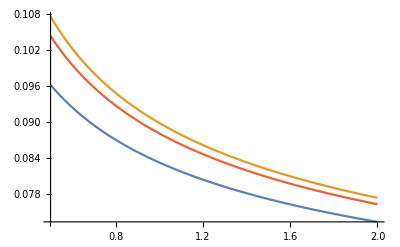

```mathematica
Plot[{αs1Loop[μ],αs2Loop[μ],αs3Loop[μ],αs[μ]},{μ,.5,2}]
```

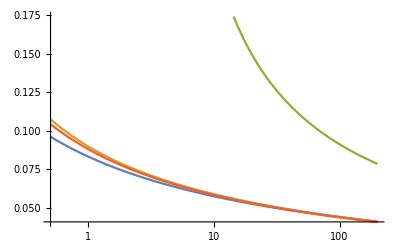

```mathematica
LogLinearPlot[{αs1Loop[μ],αs2Loop[μ],αs3Loop[μ],αs[μ]},{μ,.5,200}]
```

#### alpha tables

```mathematica
μoΛTab=1/{.19,.15,.11,.07,.046,.044,.02,.005,.001,.0006,.0005,.0003,.0001,.00003,.00001}
```

{5.26316,6.66667,9.09091,14.2857,21.7391,22.7273,50.,200.,1000.,1666.67,2000.,3333.33,10000.,33333.3,100000.}

```mathematica
nfTab=Table[0,{n,Length[μoΛTab]}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Length[nfTab]
```

15

```mathematica
ΛQCDTab=Table[ΛQCD[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD3LoopTab=Table[ΛQCD3Loop[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD2LoopTab=Table[ΛQCD2Loop[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD1LoopTab=Table[ΛQCD1Loop[nfTab[[n]]],{n,Length[nfTab]}]
```

{-0.0201654,-0.0201654,-0.0201654,-0.0201654,-0.0201654,-0.0201654,-0.0201654,-0.0201654,-0.0201654,-0.0201654,-0.0201654,-0.0201654,-0.0201654,-0.0201654,-0.0201654}

{2.26665,2.26665,2.26665,2.26665,2.26665,2.26665,2.26665,2.26665,2.26665,2.26665,2.26665,2.26665,2.26665,2.26665,2.26665}

{0.0231337,0.0231337,0.0231337,0.0231337,0.0231337,0.0231337,0.0231337,0.0231337,0.0231337,0.0231337,0.0231337,0.0231337,0.0231337,0.0231337,0.0231337}

{-0.00581807,-0.00581807,-0.00581807,-0.00581807,-0.00581807,-0.00581807,-0.00581807,-0.00581807,-0.00581807,-0.00581807,-0.00581807,-0.00581807,-0.00581807,-0.00581807,-0.00581807}

```mathematica
μGeVTab=μoΛTab ΛQCDTab
```

{-0.106134,-0.134436,-0.183322,-0.288078,-0.438379,-0.458305,-1.00827,-4.03309,-20.1654,-33.609,-40.3309,-67.2181,-201.654,-672.181,-2016.54}

```mathematica
μGeV3LoopTab=μoΛTab ΛQCD3LoopTab
```

{11.9298,15.111,20.6059,32.3808,49.2751,51.5149,113.333,453.331,2266.65,3777.76,4533.31,7555.51,22666.5,75555.1,226665.}

```mathematica
μGeV2LoopTab=μoΛTab ΛQCD2LoopTab
```

{0.121756,0.154224,0.210306,0.330481,0.502906,0.525765,1.15668,4.62673,23.1337,38.5561,46.2673,77.1122,231.337,771.122,2313.37}

```mathematica
μGeV1LoopTab=μoΛTab ΛQCD1LoopTab
```

{-0.0306214,-0.0387871,-0.0528915,-0.0831152,-0.12648,-0.132229,-0.290903,-1.16361,-5.81807,-9.69678,-11.6361,-19.3936,-58.1807,-193.936,-581.807}

```mathematica
α4Tab=Table[{μoΛTab[[n]],αs[μGeVTab[[n]]]},{n,Length[nfTab]}]
```

(5.26316 | 0.17818
6.66667 | 0.161199
9.09091 | 0.142901
14.2857 | 0.122471
21.7391 | 0.108139
22.7273 | 0.106819
50. | 0.087909
200. | 0.0672807
1000. | 0.0530493
1666.67 | 0.0497367
2000. | 0.0486546
3333.33 | 0.0458643
10000. | 0.0408464
33333.3 | 0.0364915
100000. | 0.0332673)

```mathematica
α3Tab=Table[{μoΛTab[[n]],αs3Loop[μGeV3LoopTab[[n]]]},{n,Length[nfTab]}]
```

(5.26316 | 0.191846
6.66667 | 0.16956
9.09091 | 0.14776
14.2857 | 0.12503
21.7391 | 0.109717
22.7273 | 0.108326
50. | 0.0886496
200. | 0.0675768
1000. | 0.0531844
1666.67 | 0.0498461
2000. | 0.0487565
3333.33 | 0.0459484
10000. | 0.0409041
33333.3 | 0.0365316
100000. | 0.033297)

```mathematica
α2Tab=Table[{μoΛTab[[n]],αs2Loop[μGeV2LoopTab[[n]]]},{n,Length[nfTab]}]
```

(5.26316 | 0.190914
6.66667 | 0.167641
9.09091 | 0.14531
14.2857 | 0.122513
21.7391 | 0.107404
22.7273 | 0.106039
50. | 0.0868545
200. | 0.0664298
1000. | 0.0524645
1666.67 | 0.0492165
2000. | 0.0481553
3333.33 | 0.0454183
10000. | 0.0404922
33333.3 | 0.0362113
100000. | 0.0330375)

```mathematica
α1Tab=Table[{μoΛTab[[n]],αs1Loop[μGeV1LoopTab[[n]]]},{n,Length[nfTab]}]
```

(5.26316 | 0.257958
6.66667 | 0.225815
9.09091 | 0.194085
14.2857 | 0.161097
21.7391 | 0.139131
22.7273 | 0.137151
50. | 0.109508
200. | 0.0808557
1000. | 0.0620171
1666.67 | 0.0577468
2000. | 0.0563616
3333.33 | 0.0528123
10000. | 0.0465128
33333.3 | 0.0411356
100000. | 0.0372103)

```mathematica
α4Tab[[All,2]]
```

{0.17818,0.161199,0.142901,0.122471,0.108139,0.106819,0.087909,0.0672807,0.0530493,0.0497367,0.0486546,0.0458643,0.0408464,0.0364915,0.0332673}

```mathematica
<<MaTeX`
```

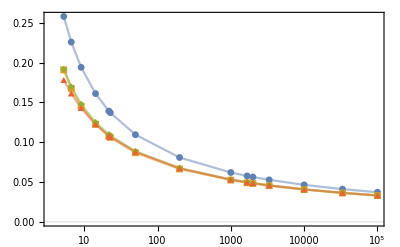

```mathematica
Show[ListLogLinearPlot[{α1Tab,α2Tab,α3Tab,α4Tab},PlotStyle->{Opacity[.5]},Joined->True],ListLogLinearPlot[{α1Tab,α2Tab,α3Tab,α4Tab},PlotMarkers->{Automatic, Small}],BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],Frame->True,Axes->False,GridLines->{{0},{0}},FrameLabel->{MaTeX["\\mu/\\Lambda_{QCD}",Magnification->1.2],MaTeX["\\alpha_s(\\mu/\\Lambda_{QCD})",Magnification->1.2]}]
```

### Nd=5

#### Running

```mathematica
(* beta function coefficients and 4-loop Lambda_QCD taken from arxiv/0908.1135 *)
```

```mathematica
β0N=beta0/.N:>5;
β1N=beta1/.N:>5;
β2N=beta2/.N:>5;
β3N=beta3/.N:>5;
Mt=173.34;Mb=4.7;Mc=1.5;
ΛQCD[f_]:=Piecewise[{{.2,f==0},{.338,f==3},{.296,f==4},{.213,f==5},{.090,f==6}}]
LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]
αsNf[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
Mαs[Q_,f_]:=1(*+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3*)
αs[Q_]:=Piecewise[{{Mαs[Mc,4]Mαs[Mb,5]αsNf[1,0],Q<1},{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,0],1≤Q<Mc},{Mαs[Mb,5]αsNf[Q,0],Mc≤Q<Mb},{αsNf[Q,0],Mb≤Q<Mt},{(1/Mαs[Mt,6])αsNf[Q,0],Q≥Mt}}]*3/N /.N:>5
αs[3]
```

0.0579049

```mathematica
MZ=91.1876;
```

```mathematica
αs[MZ]
```

0.0283839

```mathematica
(*LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]*)
LQs[Q_,f_]:=Log[Q^2/Λ^2]
αsNf4Loop[Q_,f_]:=(1/(β0N LQs[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2)+1/(β0N^3 LQs[Q,f]^3)(β1N^2/β0N^2(Log[LQs[Q,f]]^2-Log[LQs[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQs[Q,f]^4)(β1N^3/β0N^3(-Log[LQs[Q,f]]^3+(5/2)Log[LQs[Q,f]]^2+2Log[LQs[Q,f]]-1/2))-1/(β0N^4 LQs[Q,f]^4)(3β1N β2N Log[LQs[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf3Loop[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQs[Q,f]]^2-Log[LQs[Q,f]]-1)+β2N/β0N))/.Nf->f
αsNf2Loop[Q_,f_]:=(1/(β0N LQs[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2))/.Nf->f
αsNf1Loop[Q_,f_]:=(1/(β0N LQs[Q,f]))/.Nf->f
Mαs3Loop[Q_,f_]:=1(*+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3*)
Mαs2Loop[Q_,f_]:=1(*+(-.291667 )(αsNf[Q,f]/π)^2*)
αs4Loop[Q_]:=Piecewise[{{Mαs3Loop[Mc,4]Mαs3Loop[Mb,5]αsNf4Loop[Q,0],Q<1},{Mαs3Loop[Mc,4]Mαs3Loop[Mb,5]αsNf4Loop[Q,0],1≤Q<Mc},{Mαs3Loop[Mb,5]αsNf4Loop[Q,0],Mc≤Q<Mb},{αsNf4Loop[Q,0],Mb≤Q<Mt},{(1/Mαs3Loop[Mt,6])αsNf4Loop[Q,0],Q≥Mt}}]
αs3Loop[Q_]:=Piecewise[{{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,0],Q<1},{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,0],1≤Q<Mc},{Mαs2Loop[Mb,5]αsNf3Loop[Q,0],Mc≤Q<Mb},{αsNf3Loop[Q,0],Mb≤Q<Mt},{(1/Mαs2Loop[Mt,6])αsNf3Loop[Q,0],Q≥Mt}}]
αs2Loop[Q_]:=Piecewise[{{αsNf2Loop[Q,0],Q<1},{αsNf2Loop[Q,0],1≤Q<Mc},{αsNf2Loop[Q,0],Mc≤Q<Mb},{αsNf2Loop[Q,0],Mb≤Q<Mt},{αsNf2Loop[Q,0],Q≥Mt}}]
αs1Loop[Q_]:=Piecewise[{{αsNf1Loop[Q,0],Q<1},{αsNf1Loop[Q,0],1≤Q<Mc},{αsNf1Loop[Q,0],Mc≤Q<Mb},{αsNf1Loop[Q,0],Mb≤Q<Mt},{αsNf1Loop[Q,0],Q≥Mt}}]
```

```mathematica
Λ4LoopNf0=Λ/.FindRoot[αsNf4Loop[MZ,0]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

-0.00198077

```mathematica
Λ3LoopNf0=Λ/.FindRoot[αsNf3Loop[MZ,0]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

4.33066

```mathematica
Λ2LoopNf0=Λ/.FindRoot[αsNf2Loop[MZ,0]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.00225168

```mathematica
Λ1LoopNf0=Λ/.FindRoot[αsNf1Loop[MZ,0]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.000520086

```mathematica
(* don't freeze out evolution for Q < 1 GeV *)
```

```mathematica
β0N=beta0/.N:>5;
β1N=beta1/.N:>5;
β2N=beta2/.N:>5;
β3N=beta3/.N:>5;
Mt=173.34;Mb=4.7;Mc=1.5;
ΛQCD[f_]:=Λ4LoopNf0
ΛQCD3Loop[f_]:=Λ3LoopNf0
ΛQCD2Loop[f_]:=Λ2LoopNf0
ΛQCD1Loop[f_]:=Λ1LoopNf0
LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]
LQ3Loop[Q_,f_]:=Log[Q^2/ΛQCD3Loop[f]^2]
LQ2Loop[Q_,f_]:=Log[Q^2/ΛQCD2Loop[f]^2]
LQ1Loop[Q_,f_]:=Log[Q^2/ΛQCD1Loop[f]^2]
αsNf[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf4Loop[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf3Loop[Q_,f_]:=(1/(β0N LQ3Loop[Q,f])-β1N Log[LQ3Loop[Q,f]]/(β0N^3LQ3Loop[Q,f]^2)+1/(β0N^3 LQ3Loop[Q,f]^3)(β1N^2/β0N^2(Log[LQ3Loop[Q,f]]^2-Log[LQ3Loop[Q,f]]-1)+β2N/β0N))/.Nf->f
αsNf2Loop[Q_,f_]:=(1/(β0N LQ2Loop[Q,f])-β1N Log[LQ2Loop[Q,f]]/(β0N^3LQ[Q,f]^2))/.Nf->f
αsNf1Loop[Q_,f_]:=(1/(β0N LQ1Loop[Q,f]))/.Nf->f
Mαs[Q_,f_]:=1(*+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3*)
Mαs2Loop[Q_,f_]:=1(*+(-.291667 )(αsNf3Loop[Q,f]/π)^2*)
αs[Q_]:=Piecewise[{{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,0],Q<1},{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,0],1≤Q<Mc},{Mαs[Mb,5]αsNf[Q,0],Mc≤Q<Mb},{αsNf[Q,0],Mb≤Q<Mt},{(1/Mαs[Mt,6])αsNf[Q,0],Q≥Mt}}]
αs3Loop[Q_]:=Piecewise[{{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,0],Q<1},{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,0],1≤Q<Mc},{Mαs2Loop[Mb,5]αsNf3Loop[Q,0],Mc≤Q<Mb},{αsNf3Loop[Q,0],Mb≤Q<Mt},{(1/Mαs2Loop[Mt,6])αsNf3Loop[Q,0],Q≥Mt}}]
αs2Loop[Q_]:=Piecewise[{{αsNf2Loop[Q,0],Q<1},{αsNf2Loop[Q,0],1≤Q<Mc},{αsNf2Loop[Q,0],Mc≤Q<Mb},{αsNf2Loop[Q,0],Mb≤Q<Mt},{αsNf2Loop[Q,0],Q≥Mt}}]
αs1Loop[Q_]:=Piecewise[{{αsNf1Loop[Q,0],Q<1},{αsNf1Loop[Q,0],1≤Q<Mc},{αsNf1Loop[Q,0],Mc≤Q<Mb},{αsNf1Loop[Q,0],Mb≤Q<Mt},{αsNf1Loop[Q,0],Q≥Mt}}]
αs[2]
αs3Loop[2]
αs2Loop[2]
αs1Loop[2]
```

0.0423865

0.719294-0.70649 ⅈ

0.0426054

0.0415183

```mathematica
μoΛTab=1/{.95,.75,.5,.25,.05,.01,.001}
```

{1.05263,1.33333,2.,4.,20.,100.,1000.}

```mathematica
Mc/ΛQCD3Loop[4]
Mc/ΛQCD2Loop[4]
Mc/ΛQCD1Loop[4]
```

0.346368

666.169

2884.14

```mathematica
Mb/ΛQCD3Loop[5]
Mb/ΛQCD2Loop[5]
Mb/ΛQCD1Loop[5]
```

1.08529

2087.33

9036.96

```mathematica
Mt/ΛQCD3Loop[6]
Mt/ΛQCD2Loop[6]
Mt/ΛQCD1Loop[6]
```

40.0262

76982.5

333291.

```mathematica
nfTab={0,0,0,0,0,0,0};
```

```mathematica
ΛQCDTab=Table[ΛQCD[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD3LoopTab=Table[ΛQCD3Loop[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD2LoopTab=Table[ΛQCD2Loop[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD1LoopTab=Table[ΛQCD1Loop[nfTab[[n]]],{n,Length[nfTab]}]
```

{-0.00198077,-0.00198077,-0.00198077,-0.00198077,-0.00198077,-0.00198077,-0.00198077}

{4.33066,4.33066,4.33066,4.33066,4.33066,4.33066,4.33066}

{0.00225168,0.00225168,0.00225168,0.00225168,0.00225168,0.00225168,0.00225168}

{0.000520086,0.000520086,0.000520086,0.000520086,0.000520086,0.000520086,0.000520086}

```mathematica
μGeVTab=μoΛTab ΛQCDTab
```

{-0.00208502,-0.00264103,-0.00396154,-0.00792309,-0.0396154,-0.198077,-1.98077}

```mathematica
μGeV3LoopTab=μoΛTab ΛQCD3LoopTab
```

{4.55859,5.77421,8.66132,17.3226,86.6132,433.066,4330.66}

```mathematica
μGeV2LoopTab=μoΛTab ΛQCD2LoopTab
```

{0.00237019,0.00300224,0.00450336,0.00900672,0.0450336,0.225168,2.25168}

```mathematica
μGeV1LoopTab=μoΛTab ΛQCD1LoopTab
```

{0.000547459,0.000693449,0.00104017,0.00208035,0.0104017,0.0520086,0.520086}

```mathematica
Table[αs[μGeVTab[[n]]],{n,Length[nfTab]}]
```

{109382.,6.77677,0.157231,0.161331,0.0885787,0.0609465,0.04244}

```mathematica
Table[αs3Loop[μGeV3LoopTab[[n]]],{n,Length[nfTab]}]
```

{3728.46,5.65597,0.449324,0.182692,0.0899454,0.0613044,0.0425475}

```mathematica
Table[αs2Loop[μGeV2LoopTab[[n]]],{n,Length[nfTab]}]
```

{16.8921,1.65299,0.424497,0.182995,0.0879018,0.0601052,0.0419517}

```mathematica
Table[αs1Loop[μGeV1LoopTab[[n]]],{n,Length[nfTab]}]
```

{6.68156,1.19131,0.494439,0.24722,0.114402,0.0744205,0.0496137}

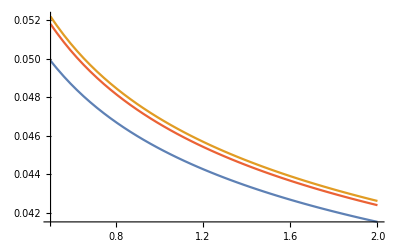

```mathematica
Plot[{αs1Loop[μ],αs2Loop[μ],αs3Loop[μ],αs[μ]},{μ,.5,2}]
```

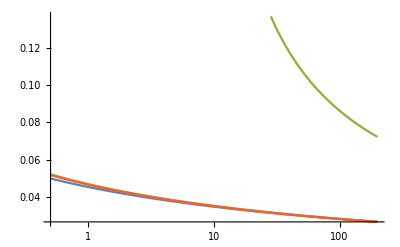

```mathematica
LogLinearPlot[{αs1Loop[μ],αs2Loop[μ],αs3Loop[μ],αs[μ]},{μ,.5,200}]
```

#### alpha tables

```mathematica
μoΛTab=1/{.19,.15,.11,.07,.046,.044,.02,.005,.001,.0006,.0005,.0003,.0001,.00003,.00001}
```

{5.26316,6.66667,9.09091,14.2857,21.7391,22.7273,50.,200.,1000.,1666.67,2000.,3333.33,10000.,33333.3,100000.}

```mathematica
nfTab=Table[0,{n,Length[μoΛTab]}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Length[nfTab]
```

15

```mathematica
ΛQCDTab=Table[ΛQCD[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD3LoopTab=Table[ΛQCD3Loop[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD2LoopTab=Table[ΛQCD2Loop[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD1LoopTab=Table[ΛQCD1Loop[nfTab[[n]]],{n,Length[nfTab]}]
```

{-0.00198077,-0.00198077,-0.00198077,-0.00198077,-0.00198077,-0.00198077,-0.00198077,-0.00198077,-0.00198077,-0.00198077,-0.00198077,-0.00198077,-0.00198077,-0.00198077,-0.00198077}

{4.33066,4.33066,4.33066,4.33066,4.33066,4.33066,4.33066,4.33066,4.33066,4.33066,4.33066,4.33066,4.33066,4.33066,4.33066}

{0.00225168,0.00225168,0.00225168,0.00225168,0.00225168,0.00225168,0.00225168,0.00225168,0.00225168,0.00225168,0.00225168,0.00225168,0.00225168,0.00225168,0.00225168}

{0.000520086,0.000520086,0.000520086,0.000520086,0.000520086,0.000520086,0.000520086,0.000520086,0.000520086,0.000520086,0.000520086,0.000520086,0.000520086,0.000520086,0.000520086}

```mathematica
μGeVTab=μoΛTab ΛQCDTab
```

{-0.0104251,-0.0132051,-0.018007,-0.0282967,-0.0430603,-0.0450175,-0.0990386,-0.396154,-1.98077,-3.30129,-3.96154,-6.60257,-19.8077,-66.0257,-198.077}

```mathematica
μGeV3LoopTab=μoΛTab ΛQCD3LoopTab
```

{22.7929,28.8711,39.3696,61.8666,94.1448,98.4241,216.533,866.132,4330.66,7217.77,8661.32,14435.5,43306.6,144355.,433066.}

```mathematica
μGeV2LoopTab=μoΛTab ΛQCD2LoopTab
```

{0.0118509,0.0150112,0.0204698,0.0321669,0.0489496,0.0511745,0.112584,0.450336,2.25168,3.7528,4.50336,7.5056,22.5168,75.056,225.168}

```mathematica
μGeV1LoopTab=μoΛTab ΛQCD1LoopTab
```

{0.0027373,0.00346724,0.00472806,0.00742981,0.0113062,0.0118201,0.0260043,0.104017,0.520086,0.866811,1.04017,1.73362,5.20086,17.3362,52.0086}

```mathematica
α4Tab=Table[{μoΛTab[[n]],αs[μGeVTab[[n]]]},{n,Length[nfTab]}]
```

(5.26316 | 0.142687
6.66667 | 0.129044
9.09091 | 0.114367
14.2857 | 0.0979985
21.7391 | 0.0865231
22.7273 | 0.0854667
50. | 0.0703318
200. | 0.053826
1000. | 0.04244
1666.67 | 0.0397897
2000. | 0.038924
3333.33 | 0.0366917
10000. | 0.0326772
33333.3 | 0.0291933
100000. | 0.0266139)

```mathematica
α3Tab=Table[{μoΛTab[[n]],αs3Loop[μGeV3LoopTab[[n]]]},{n,Length[nfTab]}]
```

(5.26316 | 0.153477
6.66667 | 0.135648
9.09091 | 0.118208
14.2857 | 0.100024
21.7391 | 0.0877733
22.7273 | 0.0866604
50. | 0.0709197
200. | 0.0540614
1000. | 0.0425475
1666.67 | 0.0398769
2000. | 0.0390052
3333.33 | 0.0367587
10000. | 0.0327233
33333.3 | 0.0292253
100000. | 0.0266376)

```mathematica
α2Tab=Table[{μoΛTab[[n]],αs2Loop[μGeV2LoopTab[[n]]]},{n,Length[nfTab]}]
```

(5.26316 | 0.152183
6.66667 | 0.133692
9.09091 | 0.115942
14.2857 | 0.097808
21.7391 | 0.0857783
22.7273 | 0.0846916
50. | 0.0694016
200. | 0.0531049
1000. | 0.0419517
1666.67 | 0.0393567
2000. | 0.0385087
3333.33 | 0.0363215
10000. | 0.0323844
33333.3 | 0.0289622
100000. | 0.0264248)

```mathematica
α1Tab=Table[{μoΛTab[[n]],αs1Loop[μGeV1LoopTab[[n]]]},{n,Length[nfTab]}]
```

(5.26316 | 0.206366
6.66667 | 0.180652
9.09091 | 0.155268
14.2857 | 0.128878
21.7391 | 0.111304
22.7273 | 0.109721
50. | 0.0876066
200. | 0.0646845
1000. | 0.0496137
1666.67 | 0.0461974
2000. | 0.0450893
3333.33 | 0.0422498
10000. | 0.0372103
33333.3 | 0.0329085
100000. | 0.0297682)

```mathematica
α4Tab[[All,2]]
```

{0.142687,0.129044,0.114367,0.0979985,0.0865231,0.0854667,0.0703318,0.053826,0.04244,0.0397897,0.038924,0.0366917,0.0326772,0.0291933,0.0266139}

```mathematica
<<MaTeX`
```

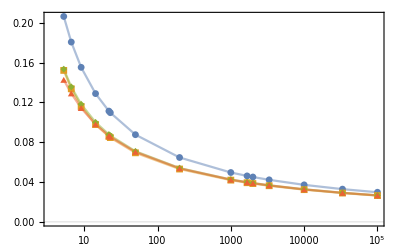

```mathematica
Show[ListLogLinearPlot[{α1Tab,α2Tab,α3Tab,α4Tab},PlotStyle->{Opacity[.5]},Joined->True],ListLogLinearPlot[{α1Tab,α2Tab,α3Tab,α4Tab},PlotMarkers->{Automatic, Small}],BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],Frame->True,Axes->False,GridLines->{{0},{0}},FrameLabel->{MaTeX["\\mu/\\Lambda_{QCD}",Magnification->1.2],MaTeX["\\alpha_s(\\mu/\\Lambda_{QCD})",Magnification->1.2]}]
```

### Nd=6

#### Running

```mathematica
(* beta function coefficients and 4-loop Lambda_QCD taken from arxiv/0908.1135 *)
```

```mathematica
β0N=beta0/.N:>6;
β1N=beta1/.N:>6;
β2N=beta2/.N:>6;
β3N=beta3/.N:>6;
Mt=173.34;Mb=4.7;Mc=1.5;
ΛQCD[f_]:=Piecewise[{{.2,f==0},{.338,f==3},{.296,f==4},{.213,f==5},{.090,f==6}}]
LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]
αsNf[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
Mαs[Q_,f_]:=1(*+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3*)
αs[Q_]:=Piecewise[{{Mαs[Mc,4]Mαs[Mb,5]αsNf[1,0],Q<1},{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,0],1≤Q<Mc},{Mαs[Mb,5]αsNf[Q,0],Mc≤Q<Mb},{αsNf[Q,0],Mb≤Q<Mt},{(1/Mαs[Mt,6])αsNf[Q,0],Q≥Mt}}]*3/N /.N:>6
αs[3]
```

0.0402163

```mathematica
MZ=91.1876;
```

```mathematica
αs[MZ]
```

0.0197112

```mathematica
(*LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]*)
LQs[Q_,f_]:=Log[Q^2/Λ^2]
αsNf4Loop[Q_,f_]:=(1/(β0N LQs[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2)+1/(β0N^3 LQs[Q,f]^3)(β1N^2/β0N^2(Log[LQs[Q,f]]^2-Log[LQs[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQs[Q,f]^4)(β1N^3/β0N^3(-Log[LQs[Q,f]]^3+(5/2)Log[LQs[Q,f]]^2+2Log[LQs[Q,f]]-1/2))-1/(β0N^4 LQs[Q,f]^4)(3β1N β2N Log[LQs[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf3Loop[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQs[Q,f]]^2-Log[LQs[Q,f]]-1)+β2N/β0N))/.Nf->f
αsNf2Loop[Q_,f_]:=(1/(β0N LQs[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2))/.Nf->f
αsNf1Loop[Q_,f_]:=(1/(β0N LQs[Q,f]))/.Nf->f
Mαs3Loop[Q_,f_]:=1(*+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3*)
Mαs2Loop[Q_,f_]:=1(*+(-.291667 )(αsNf[Q,f]/π)^2*)
αs4Loop[Q_]:=Piecewise[{{Mαs3Loop[Mc,4]Mαs3Loop[Mb,5]αsNf4Loop[Q,0],Q<1},{Mαs3Loop[Mc,4]Mαs3Loop[Mb,5]αsNf4Loop[Q,0],1≤Q<Mc},{Mαs3Loop[Mb,5]αsNf4Loop[Q,0],Mc≤Q<Mb},{αsNf4Loop[Q,0],Mb≤Q<Mt},{(1/Mαs3Loop[Mt,6])αsNf4Loop[Q,0],Q≥Mt}}]
αs3Loop[Q_]:=Piecewise[{{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,0],Q<1},{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,0],1≤Q<Mc},{Mαs2Loop[Mb,5]αsNf3Loop[Q,0],Mc≤Q<Mb},{αsNf3Loop[Q,0],Mb≤Q<Mt},{(1/Mαs2Loop[Mt,6])αsNf3Loop[Q,0],Q≥Mt}}]
αs2Loop[Q_]:=Piecewise[{{αsNf2Loop[Q,0],Q<1},{αsNf2Loop[Q,0],1≤Q<Mc},{αsNf2Loop[Q,0],Mc≤Q<Mb},{αsNf2Loop[Q,0],Mb≤Q<Mt},{αsNf2Loop[Q,0],Q≥Mt}}]
αs1Loop[Q_]:=Piecewise[{{αsNf1Loop[Q,0],Q<1},{αsNf1Loop[Q,0],1≤Q<Mc},{αsNf1Loop[Q,0],Mc≤Q<Mb},{αsNf1Loop[Q,0],Mb≤Q<Mt},{αsNf1Loop[Q,0],Q≥Mt}}]
```

```mathematica
Λ4LoopNf0=Λ/.FindRoot[αsNf4Loop[MZ,0]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.000191277

```mathematica
Λ3LoopNf0=Λ/.FindRoot[αsNf3Loop[MZ,0]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

5.90391

```mathematica
Λ2LoopNf0=Λ/.FindRoot[αsNf2Loop[MZ,0]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.000215612

```mathematica
Λ1LoopNf0=Λ/.FindRoot[αsNf1Loop[MZ,0]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.00004649

```mathematica
(* don't freeze out evolution for Q < 1 GeV *)
```

```mathematica
β0N=beta0/.N:>6;
β1N=beta1/.N:>6;
β2N=beta2/.N:>6;
β3N=beta3/.N:>6;
Mt=173.34;Mb=4.7;Mc=1.5;
ΛQCD[f_]:=Λ4LoopNf0
ΛQCD3Loop[f_]:=Λ3LoopNf0
ΛQCD2Loop[f_]:=Λ2LoopNf0
ΛQCD1Loop[f_]:=Λ1LoopNf0
LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]
LQ3Loop[Q_,f_]:=Log[Q^2/ΛQCD3Loop[f]^2]
LQ2Loop[Q_,f_]:=Log[Q^2/ΛQCD2Loop[f]^2]
LQ1Loop[Q_,f_]:=Log[Q^2/ΛQCD1Loop[f]^2]
αsNf[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf4Loop[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf3Loop[Q_,f_]:=(1/(β0N LQ3Loop[Q,f])-β1N Log[LQ3Loop[Q,f]]/(β0N^3LQ3Loop[Q,f]^2)+1/(β0N^3 LQ3Loop[Q,f]^3)(β1N^2/β0N^2(Log[LQ3Loop[Q,f]]^2-Log[LQ3Loop[Q,f]]-1)+β2N/β0N))/.Nf->f
αsNf2Loop[Q_,f_]:=(1/(β0N LQ2Loop[Q,f])-β1N Log[LQ2Loop[Q,f]]/(β0N^3LQ[Q,f]^2))/.Nf->f
αsNf1Loop[Q_,f_]:=(1/(β0N LQ1Loop[Q,f]))/.Nf->f
Mαs[Q_,f_]:=1(*+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3*)
Mαs2Loop[Q_,f_]:=1(*+(-.291667 )(αsNf3Loop[Q,f]/π)^2*)
αs[Q_]:=Piecewise[{{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,0],Q<1},{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,0],1≤Q<Mc},{Mαs[Mb,5]αsNf[Q,0],Mc≤Q<Mb},{αsNf[Q,0],Mb≤Q<Mt},{(1/Mαs[Mt,6])αsNf[Q,0],Q≥Mt}}]
αs3Loop[Q_]:=Piecewise[{{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,0],Q<1},{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,0],1≤Q<Mc},{Mαs2Loop[Mb,5]αsNf3Loop[Q,0],Mc≤Q<Mb},{αsNf3Loop[Q,0],Mb≤Q<Mt},{(1/Mαs2Loop[Mt,6])αsNf3Loop[Q,0],Q≥Mt}}]
αs2Loop[Q_]:=Piecewise[{{αsNf2Loop[Q,0],Q<1},{αsNf2Loop[Q,0],1≤Q<Mc},{αsNf2Loop[Q,0],Mc≤Q<Mb},{αsNf2Loop[Q,0],Mb≤Q<Mt},{αsNf2Loop[Q,0],Q≥Mt}}]
αs1Loop[Q_]:=Piecewise[{{αsNf1Loop[Q,0],Q<1},{αsNf1Loop[Q,0],1≤Q<Mc},{αsNf1Loop[Q,0],Mc≤Q<Mb},{αsNf1Loop[Q,0],Mb≤Q<Mt},{αsNf1Loop[Q,0],Q≥Mt}}]
αs[2]
αs3Loop[2]
αs2Loop[2]
αs1Loop[2]
```

0.027111

0.0382313-0.39121 ⅈ

0.0271807

0.026768

```mathematica
μoΛTab=1/{.95,.75,.5,.25,.05,.01,.001}
```

{1.05263,1.33333,2.,4.,20.,100.,1000.}

```mathematica
Mc/ΛQCD3Loop[4]
Mc/ΛQCD2Loop[4]
Mc/ΛQCD1Loop[4]
```

0.254069

6956.94

32265.

```mathematica
Mb/ΛQCD3Loop[5]
Mb/ΛQCD2Loop[5]
Mb/ΛQCD1Loop[5]
```

0.796083

21798.4

101097.

```mathematica
Mt/ΛQCD3Loop[6]
Mt/ΛQCD2Loop[6]
Mt/ΛQCD1Loop[6]
```

29.3602

803944.

3.72854×10^6

```mathematica
nfTab={0,0,0,0,0,0,0};
```

```mathematica
ΛQCDTab=Table[ΛQCD[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD3LoopTab=Table[ΛQCD3Loop[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD2LoopTab=Table[ΛQCD2Loop[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD1LoopTab=Table[ΛQCD1Loop[nfTab[[n]]],{n,Length[nfTab]}]
```

{0.000191277,0.000191277,0.000191277,0.000191277,0.000191277,0.000191277,0.000191277}

{5.90391,5.90391,5.90391,5.90391,5.90391,5.90391,5.90391}

{0.000215612,0.000215612,0.000215612,0.000215612,0.000215612,0.000215612,0.000215612}

{0.00004649,0.00004649,0.00004649,0.00004649,0.00004649,0.00004649,0.00004649}

```mathematica
μGeVTab=μoΛTab ΛQCDTab
```

{0.000201344,0.000255036,0.000382553,0.000765107,0.00382553,0.0191277,0.191277}

```mathematica
μGeV3LoopTab=μoΛTab ΛQCD3LoopTab
```

{6.21464,7.87188,11.8078,23.6156,118.078,590.391,5903.91}

```mathematica
μGeV2LoopTab=μoΛTab ΛQCD2LoopTab
```

{0.00022696,0.000287483,0.000431224,0.000862448,0.00431224,0.0215612,0.215612}

```mathematica
μGeV1LoopTab=μoΛTab ΛQCD1LoopTab
```

{0.0000489369,0.0000619867,0.00009298,0.00018596,0.0009298,0.004649,0.04649}

```mathematica
Table[αs[μGeVTab[[n]]],{n,Length[nfTab]}]
```

{91223.4,5.71952,0.133169,0.134577,0.0738217,0.0507898,0.0353668}

```mathematica
Table[αs3Loop[μGeV3LoopTab[[n]]],{n,Length[nfTab]}]
```

{3107.05,4.7133,0.374437,0.152243,0.0749545,0.051087,0.0354563}

```mathematica
Table[αs2Loop[μGeV2LoopTab[[n]]],{n,Length[nfTab]}]
```

{14.9361,1.39357,0.352532,0.151895,0.0731318,0.0500451,0.0349445}

```mathematica
Table[αs1Loop[μGeV1LoopTab[[n]]],{n,Length[nfTab]}]
```

{5.56797,0.99276,0.412033,0.206016,0.0953354,0.0620171,0.0413447}

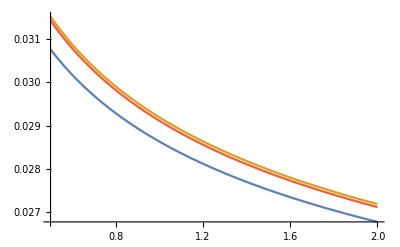

```mathematica
Plot[{αs1Loop[μ],αs2Loop[μ],αs3Loop[μ],αs[μ]},{μ,.5,2}]
```

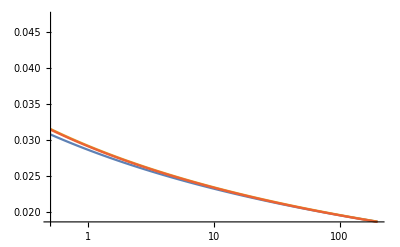

```mathematica
LogLinearPlot[{αs1Loop[μ],αs2Loop[μ],αs3Loop[μ],αs[μ]},{μ,.5,200}]
```

#### alpha tables

```mathematica
μoΛTab=1/{.19,.15,.11,.07,.046,.044,.02,.005,.001,.0006,.0005,.0003,.0001,.00003,.00001}
```

{5.26316,6.66667,9.09091,14.2857,21.7391,22.7273,50.,200.,1000.,1666.67,2000.,3333.33,10000.,33333.3,100000.}

```mathematica
nfTab=Table[0,{n,Length[μoΛTab]}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Length[nfTab]
```

15

```mathematica
ΛQCDTab=Table[ΛQCD[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD3LoopTab=Table[ΛQCD3Loop[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD2LoopTab=Table[ΛQCD2Loop[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD1LoopTab=Table[ΛQCD1Loop[nfTab[[n]]],{n,Length[nfTab]}]
```

{0.000191277,0.000191277,0.000191277,0.000191277,0.000191277,0.000191277,0.000191277,0.000191277,0.000191277,0.000191277,0.000191277,0.000191277,0.000191277,0.000191277,0.000191277}

{5.90391,5.90391,5.90391,5.90391,5.90391,5.90391,5.90391,5.90391,5.90391,5.90391,5.90391,5.90391,5.90391,5.90391,5.90391}

{0.000215612,0.000215612,0.000215612,0.000215612,0.000215612,0.000215612,0.000215612,0.000215612,0.000215612,0.000215612,0.000215612,0.000215612,0.000215612,0.000215612,0.000215612}

{0.00004649,0.00004649,0.00004649,0.00004649,0.00004649,0.00004649,0.00004649,0.00004649,0.00004649,0.00004649,0.00004649,0.00004649,0.00004649,0.00004649,0.00004649}

```mathematica
μGeVTab=μoΛTab ΛQCDTab
```

{0.00100672,0.00127518,0.00173888,0.00273252,0.00415819,0.0043472,0.00956384,0.0382553,0.191277,0.318795,0.382553,0.637589,1.91277,6.37589,19.1277}

```mathematica
μGeV3LoopTab=μoΛTab ΛQCD3LoopTab
```

{31.0732,39.3594,53.6719,84.3415,128.346,134.18,295.195,1180.78,5903.91,9839.85,11807.8,19679.7,59039.1,196797.,590391.}

```mathematica
μGeV2LoopTab=μoΛTab ΛQCD2LoopTab
```

{0.0011348,0.00143741,0.00196011,0.00308017,0.00468722,0.00490027,0.0107806,0.0431224,0.215612,0.359353,0.431224,0.718707,2.15612,7.18707,21.5612}

```mathematica
μGeV1LoopTab=μoΛTab ΛQCD1LoopTab
```

{0.000244684,0.000309933,0.000422636,0.000664143,0.00101065,0.00105659,0.0023245,0.009298,0.04649,0.0774834,0.09298,0.154967,0.4649,1.54967,4.649}

```mathematica
α4Tab=Table[{μoΛTab[[n]],αs[μGeVTab[[n]]]},{n,Length[nfTab]}]
```

(5.26316 | 0.118971
6.66667 | 0.107575
9.09091 | 0.0953267
14.2857 | 0.0816753
21.7391 | 0.0721081
22.7273 | 0.0712275
50. | 0.058612
200. | 0.0448556
1000. | 0.0353668
1666.67 | 0.0331582
2000. | 0.0324368
3333.33 | 0.0305765
10000. | 0.0272311
33333.3 | 0.0243278
100000. | 0.0221783)

```mathematica
α3Tab=Table[{μoΛTab[[n]],αs3Loop[μGeV3LoopTab[[n]]]},{n,Length[nfTab]}]
```

(5.26316 | 0.127897
6.66667 | 0.11304
9.09091 | 0.0985066
14.2857 | 0.0833536
21.7391 | 0.0731444
22.7273 | 0.072217
50. | 0.0590998
200. | 0.0450512
1000. | 0.0354563
1666.67 | 0.0332308
2000. | 0.0325043
3333.33 | 0.0306323
10000. | 0.0272694
33333.3 | 0.0243544
100000. | 0.022198)

```mathematica
α2Tab=Table[{μoΛTab[[n]],αs2Loop[μGeV2LoopTab[[n]]]},{n,Length[nfTab]}]
```

(5.26316 | 0.12639
6.66667 | 0.111082
9.09091 | 0.0963808
14.2857 | 0.0813494
21.7391 | 0.0713696
22.7273 | 0.0704678
50. | 0.0577712
200. | 0.0442241
1000. | 0.0349445
1666.67 | 0.0327845
2000. | 0.0320786
3333.33 | 0.0302578
10000. | 0.0269797
33333.3 | 0.0241299
100000. | 0.0220166)

```mathematica
α1Tab=Table[{μoΛTab[[n]],αs1Loop[μGeV1LoopTab[[n]]]},{n,Length[nfTab]}]
```

(5.26316 | 0.171972
6.66667 | 0.150544
9.09091 | 0.12939
14.2857 | 0.107398
21.7391 | 0.0927537
22.7273 | 0.0914338
50. | 0.0730055
200. | 0.0539038
1000. | 0.0413447
1666.67 | 0.0384978
2000. | 0.0375744
3333.33 | 0.0352082
10000. | 0.0310086
33333.3 | 0.0274237
100000. | 0.0248068)

```mathematica
α4Tab[[All,2]]
```

{0.118971,0.107575,0.0953267,0.0816753,0.0721081,0.0712275,0.058612,0.0448556,0.0353668,0.0331582,0.0324368,0.0305765,0.0272311,0.0243278,0.0221783}

```mathematica
<<MaTeX`
```

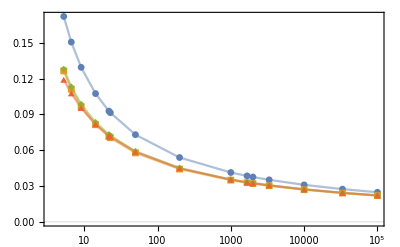

```mathematica
Show[ListLogLinearPlot[{α1Tab,α2Tab,α3Tab,α4Tab},PlotStyle->{Opacity[.5]},Joined->True],ListLogLinearPlot[{α1Tab,α2Tab,α3Tab,α4Tab},PlotMarkers->{Automatic, Small}],BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],Frame->True,Axes->False,GridLines->{{0},{0}},FrameLabel->{MaTeX["\\mu/\\Lambda_{QCD}",Magnification->1.2],MaTeX["\\alpha_s(\\mu/\\Lambda_{QCD})",Magnification->1.2]}]
```

### Nd=7

#### Running

```mathematica
(* beta function coefficients and 4-loop Lambda_QCD taken from arxiv/0908.1135 *)
```

```mathematica
β0N=beta0/.N:>7;
β1N=beta1/.N:>7;
β2N=beta2/.N:>7;
β3N=beta3/.N:>7;
Mt=173.34;Mb=4.7;Mc=1.5;
ΛQCD[f_]:=Piecewise[{{.2,f==0},{.338,f==3},{.296,f==4},{.213,f==5},{.090,f==6}}]
LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]
αsNf[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
Mαs[Q_,f_]:=1(*+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3*)
αs[Q_]:=Piecewise[{{Mαs[Mc,4]Mαs[Mb,5]αsNf[1,0],Q<1},{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,0],1≤Q<Mc},{Mαs[Mb,5]αsNf[Q,0],Mc≤Q<Mb},{αsNf[Q,0],Mb≤Q<Mt},{(1/Mαs[Mt,6])αsNf[Q,0],Q≥Mt}}]*3/N /.N:>7
αs[3]
```

0.0295487

```mathematica
MZ=91.1876;
```

```mathematica
αs[MZ]
```

0.0144818

```mathematica
(*LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]*)
LQs[Q_,f_]:=Log[Q^2/Λ^2]
αsNf4Loop[Q_,f_]:=(1/(β0N LQs[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2)+1/(β0N^3 LQs[Q,f]^3)(β1N^2/β0N^2(Log[LQs[Q,f]]^2-Log[LQs[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQs[Q,f]^4)(β1N^3/β0N^3(-Log[LQs[Q,f]]^3+(5/2)Log[LQs[Q,f]]^2+2Log[LQs[Q,f]]-1/2))-1/(β0N^4 LQs[Q,f]^4)(3β1N β2N Log[LQs[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf3Loop[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQs[Q,f]]^2-Log[LQs[Q,f]]-1)+β2N/β0N))/.Nf->f
αsNf2Loop[Q_,f_]:=(1/(β0N LQs[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2))/.Nf->f
αsNf1Loop[Q_,f_]:=(1/(β0N LQs[Q,f]))/.Nf->f
Mαs3Loop[Q_,f_]:=1(*+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3*)
Mαs2Loop[Q_,f_]:=1(*+(-.291667 )(αsNf[Q,f]/π)^2*)
αs4Loop[Q_]:=Piecewise[{{Mαs3Loop[Mc,4]Mαs3Loop[Mb,5]αsNf4Loop[Q,0],Q<1},{Mαs3Loop[Mc,4]Mαs3Loop[Mb,5]αsNf4Loop[Q,0],1≤Q<Mc},{Mαs3Loop[Mb,5]αsNf4Loop[Q,0],Mc≤Q<Mb},{αsNf4Loop[Q,0],Mb≤Q<Mt},{(1/Mαs3Loop[Mt,6])αsNf4Loop[Q,0],Q≥Mt}}]
αs3Loop[Q_]:=Piecewise[{{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,0],Q<1},{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,0],1≤Q<Mc},{Mαs2Loop[Mb,5]αsNf3Loop[Q,0],Mc≤Q<Mb},{αsNf3Loop[Q,0],Mb≤Q<Mt},{(1/Mαs2Loop[Mt,6])αsNf3Loop[Q,0],Q≥Mt}}]
αs2Loop[Q_]:=Piecewise[{{αsNf2Loop[Q,0],Q<1},{αsNf2Loop[Q,0],1≤Q<Mc},{αsNf2Loop[Q,0],Mc≤Q<Mb},{αsNf2Loop[Q,0],Mb≤Q<Mt},{αsNf2Loop[Q,0],Q≥Mt}}]
αs1Loop[Q_]:=Piecewise[{{αsNf1Loop[Q,0],Q<1},{αsNf1Loop[Q,0],1≤Q<Mc},{αsNf1Loop[Q,0],Mc≤Q<Mb},{αsNf1Loop[Q,0],Mb≤Q<Mt},{αsNf1Loop[Q,0],Q≥Mt}}]
```

```mathematica
Λ4LoopNf0=Λ/.FindRoot[αsNf4Loop[MZ,0]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.0000182527

```mathematica
Λ3LoopNf0=Λ/.FindRoot[αsNf3Loop[MZ,0]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

7.09074

```mathematica
Λ2LoopNf0=Λ/.FindRoot[αsNf2Loop[MZ,0]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.0000204231

```mathematica
Λ1LoopNf0=Λ/.FindRoot[αsNf1Loop[MZ,0]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

-4.15563×10^-6

```mathematica
(* don't freeze out evolution for Q < 1 GeV *)
```

```mathematica
β0N=beta0/.N:>6;
β1N=beta1/.N:>6;
β2N=beta2/.N:>6;
β3N=beta3/.N:>6;
Mt=173.34;Mb=4.7;Mc=1.5;
ΛQCD[f_]:=Λ4LoopNf0
ΛQCD3Loop[f_]:=Λ3LoopNf0
ΛQCD2Loop[f_]:=Λ2LoopNf0
ΛQCD1Loop[f_]:=Λ1LoopNf0
LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]
LQ3Loop[Q_,f_]:=Log[Q^2/ΛQCD3Loop[f]^2]
LQ2Loop[Q_,f_]:=Log[Q^2/ΛQCD2Loop[f]^2]
LQ1Loop[Q_,f_]:=Log[Q^2/ΛQCD1Loop[f]^2]
αsNf[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf4Loop[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf3Loop[Q_,f_]:=(1/(β0N LQ3Loop[Q,f])-β1N Log[LQ3Loop[Q,f]]/(β0N^3LQ3Loop[Q,f]^2)+1/(β0N^3 LQ3Loop[Q,f]^3)(β1N^2/β0N^2(Log[LQ3Loop[Q,f]]^2-Log[LQ3Loop[Q,f]]-1)+β2N/β0N))/.Nf->f
αsNf2Loop[Q_,f_]:=(1/(β0N LQ2Loop[Q,f])-β1N Log[LQ2Loop[Q,f]]/(β0N^3LQ[Q,f]^2))/.Nf->f
αsNf1Loop[Q_,f_]:=(1/(β0N LQ1Loop[Q,f]))/.Nf->f
Mαs[Q_,f_]:=1(*+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3*)
Mαs2Loop[Q_,f_]:=1(*+(-.291667 )(αsNf3Loop[Q,f]/π)^2*)
αs[Q_]:=Piecewise[{{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,0],Q<1},{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,0],1≤Q<Mc},{Mαs[Mb,5]αsNf[Q,0],Mc≤Q<Mb},{αsNf[Q,0],Mb≤Q<Mt},{(1/Mαs[Mt,6])αsNf[Q,0],Q≥Mt}}]
αs3Loop[Q_]:=Piecewise[{{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,0],Q<1},{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,0],1≤Q<Mc},{Mαs2Loop[Mb,5]αsNf3Loop[Q,0],Mc≤Q<Mb},{αsNf3Loop[Q,0],Mb≤Q<Mt},{(1/Mαs2Loop[Mt,6])αsNf3Loop[Q,0],Q≥Mt}}]
αs2Loop[Q_]:=Piecewise[{{αsNf2Loop[Q,0],Q<1},{αsNf2Loop[Q,0],1≤Q<Mc},{αsNf2Loop[Q,0],Mc≤Q<Mb},{αsNf2Loop[Q,0],Mb≤Q<Mt},{αsNf2Loop[Q,0],Q≥Mt}}]
αs1Loop[Q_]:=Piecewise[{{αsNf1Loop[Q,0],Q<1},{αsNf1Loop[Q,0],1≤Q<Mc},{αsNf1Loop[Q,0],Mc≤Q<Mb},{αsNf1Loop[Q,0],Mb≤Q<Mt},{αsNf1Loop[Q,0],Q≥Mt}}]
αs[2]
αs3Loop[2]
αs2Loop[2]
αs1Loop[2]
```

0.0220167

-0.0595651-0.3035 ⅈ

0.0220498

0.0218278

```mathematica
μoΛTab=1/{.95,.75,.5,.25,.05,.01,.001}
```

{1.05263,1.33333,2.,4.,20.,100.,1000.}

```mathematica
Mc/ΛQCD3Loop[4]
Mc/ΛQCD2Loop[4]
Mc/ΛQCD1Loop[4]
```

0.211544

73446.2

-360956.

```mathematica
Mb/ΛQCD3Loop[5]
Mb/ΛQCD2Loop[5]
Mb/ΛQCD1Loop[5]
```

0.662836

230131.

-1.131×10^6

```mathematica
Mt/ΛQCD3Loop[6]
Mt/ΛQCD2Loop[6]
Mt/ΛQCD1Loop[6]
```

24.446

8.48744×10^6

-4.17121×10^7

```mathematica
nfTab={0,0,0,0,0,0,0};
```

```mathematica
ΛQCDTab=Table[ΛQCD[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD3LoopTab=Table[ΛQCD3Loop[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD2LoopTab=Table[ΛQCD2Loop[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD1LoopTab=Table[ΛQCD1Loop[nfTab[[n]]],{n,Length[nfTab]}]
```

{0.0000182527,0.0000182527,0.0000182527,0.0000182527,0.0000182527,0.0000182527,0.0000182527}

{7.09074,7.09074,7.09074,7.09074,7.09074,7.09074,7.09074}

{0.0000204231,0.0000204231,0.0000204231,0.0000204231,0.0000204231,0.0000204231,0.0000204231}

{-4.15563×10^-6,-4.15563×10^-6,-4.15563×10^-6,-4.15563×10^-6,-4.15563×10^-6,-4.15563×10^-6,-4.15563×10^-6}

```mathematica
μGeVTab=μoΛTab ΛQCDTab
```

{0.0000192134,0.0000243369,0.0000365054,0.0000730108,0.000365054,0.00182527,0.0182527}

```mathematica
μGeV3LoopTab=μoΛTab ΛQCD3LoopTab
```

{7.46394,9.45432,14.1815,28.363,141.815,709.074,7090.74}

```mathematica
μGeV2LoopTab=μoΛTab ΛQCD2LoopTab
```

{0.000021498,0.0000272308,0.0000408462,0.0000816925,0.000408462,0.00204231,0.0204231}

```mathematica
μGeV1LoopTab=μoΛTab ΛQCD1LoopTab
```

{-4.37434×10^-6,-5.54084×10^-6,-8.31125×10^-6,-0.0000166225,-0.0000831125,-0.000415563,-0.00415563}

```mathematica
Table[αs[μGeVTab[[n]]],{n,Length[nfTab]}]
```

{91223.4,5.71952,0.133169,0.134577,0.0738217,0.0507898,0.0353668}

```mathematica
Table[αs3Loop[μGeV3LoopTab[[n]]],{n,Length[nfTab]}]
```

{3107.05,4.7133,0.374437,0.152243,0.0749545,0.051087,0.0354563}

```mathematica
Table[αs2Loop[μGeV2LoopTab[[n]]],{n,Length[nfTab]}]
```

{15.8031,1.40855,0.351433,0.151359,0.0730259,0.0500075,0.034931}

```mathematica
Table[αs1Loop[μGeV1LoopTab[[n]]],{n,Length[nfTab]}]
```

{5.56797,0.99276,0.412033,0.206016,0.0953354,0.0620171,0.0413447}

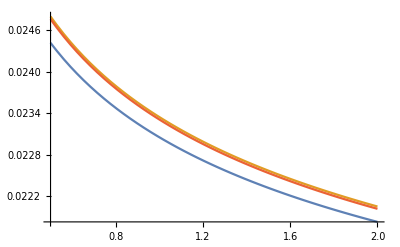

```mathematica
Plot[{αs1Loop[μ],αs2Loop[μ],αs3Loop[μ],αs[μ]},{μ,.5,2}]
```

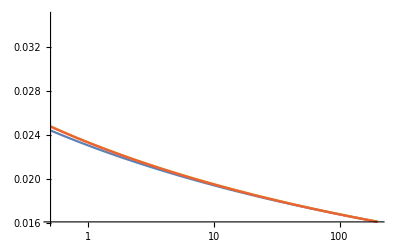

```mathematica
LogLinearPlot[{αs1Loop[μ],αs2Loop[μ],αs3Loop[μ],αs[μ]},{μ,.5,200}]
```

#### alpha tables

```mathematica
μoΛTab=1/{.19,.15,.11,.07,.046,.044,.02,.005,.001,.0006,.0005,.0003,.0001,.00003,.00001}
```

{5.26316,6.66667,9.09091,14.2857,21.7391,22.7273,50.,200.,1000.,1666.67,2000.,3333.33,10000.,33333.3,100000.}

```mathematica
nfTab=Table[0,{n,Length[μoΛTab]}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Length[nfTab]
```

15

```mathematica
ΛQCDTab=Table[ΛQCD[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD3LoopTab=Table[ΛQCD3Loop[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD2LoopTab=Table[ΛQCD2Loop[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD1LoopTab=Table[ΛQCD1Loop[nfTab[[n]]],{n,Length[nfTab]}]
```

{0.0000182527,0.0000182527,0.0000182527,0.0000182527,0.0000182527,0.0000182527,0.0000182527,0.0000182527,0.0000182527,0.0000182527,0.0000182527,0.0000182527,0.0000182527,0.0000182527,0.0000182527}

{7.09074,7.09074,7.09074,7.09074,7.09074,7.09074,7.09074,7.09074,7.09074,7.09074,7.09074,7.09074,7.09074,7.09074,7.09074}

{0.0000204231,0.0000204231,0.0000204231,0.0000204231,0.0000204231,0.0000204231,0.0000204231,0.0000204231,0.0000204231,0.0000204231,0.0000204231,0.0000204231,0.0000204231,0.0000204231,0.0000204231}

{-4.15563×10^-6,-4.15563×10^-6,-4.15563×10^-6,-4.15563×10^-6,-4.15563×10^-6,-4.15563×10^-6,-4.15563×10^-6,-4.15563×10^-6,-4.15563×10^-6,-4.15563×10^-6,-4.15563×10^-6,-4.15563×10^-6,-4.15563×10^-6,-4.15563×10^-6,-4.15563×10^-6}

```mathematica
μGeVTab=μoΛTab ΛQCDTab
```

{0.0000960669,0.000121685,0.000165934,0.000260753,0.000396798,0.000414834,0.000912635,0.00365054,0.0182527,0.0304212,0.0365054,0.0608423,0.182527,0.608423,1.82527}

```mathematica
μGeV3LoopTab=μoΛTab ΛQCD3LoopTab
```

{37.3197,47.2716,64.4613,101.296,154.146,161.153,354.537,1418.15,7090.74,11817.9,14181.5,23635.8,70907.4,236358.,709074.}

```mathematica
μGeV2LoopTab=μoΛTab ΛQCD2LoopTab
```

{0.00010749,0.000136154,0.000185665,0.000291759,0.000443981,0.000464162,0.00102116,0.00408462,0.0204231,0.0340385,0.0408462,0.0680771,0.204231,0.680771,2.04231}

```mathematica
μGeV1LoopTab=μoΛTab ΛQCD1LoopTab
```

{-0.0000218717,-0.0000277042,-0.0000377784,-0.0000593661,-0.0000903397,-0.0000944461,-0.000207781,-0.000831125,-0.00415563,-0.00692604,-0.00831125,-0.0138521,-0.0415563,-0.138521,-0.415563}

```mathematica
α4Tab=Table[{μoΛTab[[n]],αs[μGeVTab[[n]]]},{n,Length[nfTab]}]
```

(5.26316 | 0.118971
6.66667 | 0.107575
9.09091 | 0.0953267
14.2857 | 0.0816753
21.7391 | 0.0721081
22.7273 | 0.0712275
50. | 0.058612
200. | 0.0448556
1000. | 0.0353668
1666.67 | 0.0331582
2000. | 0.0324368
3333.33 | 0.0305765
10000. | 0.0272311
33333.3 | 0.0243278
100000. | 0.0221783)

```mathematica
α3Tab=Table[{μoΛTab[[n]],αs3Loop[μGeV3LoopTab[[n]]]},{n,Length[nfTab]}]
```

(5.26316 | 0.127897
6.66667 | 0.11304
9.09091 | 0.0985066
14.2857 | 0.0833536
21.7391 | 0.0731444
22.7273 | 0.072217
50. | 0.0590998
200. | 0.0450512
1000. | 0.0354563
1666.67 | 0.0332308
2000. | 0.0325043
3333.33 | 0.0306323
10000. | 0.0272694
33333.3 | 0.0243544
100000. | 0.022198)

```mathematica
α2Tab=Table[{μoΛTab[[n]],αs2Loop[μGeV2LoopTab[[n]]]},{n,Length[nfTab]}]
```

(5.26316 | 0.126009
6.66667 | 0.110791
9.09091 | 0.0961697
14.2857 | 0.08121
21.7391 | 0.0712703
22.7273 | 0.0703717
50. | 0.057715
200. | 0.0441976
1000. | 0.034931
1666.67 | 0.0327732
2000. | 0.0320681
3333.33 | 0.0302489
10000. | 0.0269733
33333.3 | 0.0241253
100000. | 0.022013)

```mathematica
α1Tab=Table[{μoΛTab[[n]],αs1Loop[μGeV1LoopTab[[n]]]},{n,Length[nfTab]}]
```

(5.26316 | 0.171972
6.66667 | 0.150544
9.09091 | 0.12939
14.2857 | 0.107398
21.7391 | 0.0927537
22.7273 | 0.0914338
50. | 0.0730055
200. | 0.0539038
1000. | 0.0413447
1666.67 | 0.0384978
2000. | 0.0375744
3333.33 | 0.0352082
10000. | 0.0310086
33333.3 | 0.0274237
100000. | 0.0248068)

```mathematica
α4Tab[[All,2]]
```

{0.118971,0.107575,0.0953267,0.0816753,0.0721081,0.0712275,0.058612,0.0448556,0.0353668,0.0331582,0.0324368,0.0305765,0.0272311,0.0243278,0.0221783}

```mathematica
<<MaTeX`
```

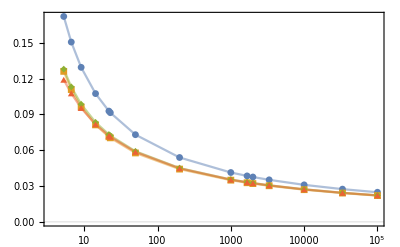

```mathematica
Show[ListLogLinearPlot[{α1Tab,α2Tab,α3Tab,α4Tab},PlotStyle->{Opacity[.5]},Joined->True],ListLogLinearPlot[{α1Tab,α2Tab,α3Tab,α4Tab},PlotMarkers->{Automatic, Small}],BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],Frame->True,Axes->False,GridLines->{{0},{0}},FrameLabel->{MaTeX["\\mu/\\Lambda_{QCD}",Magnification->1.2],MaTeX["\\alpha_s(\\mu/\\Lambda_{QCD})",Magnification->1.2]}]
```

### Nd=100

```mathematica
(* beta function coefficients and 4-loop Lambda_QCD taken from arxiv/0908.1135 *)
```

```mathematica
β0N=beta0/.N:>100;
β1N=beta1/.N:>100;
β2N=beta2/.N:>100;
β3N=beta3/.N:>100;
Mt=173.34;Mb=4.7;Mc=1.5;
ΛQCD[f_]:=Piecewise[{{.2,f==0},{.338,f==3},{.296,f==4},{.213,f==5},{.090,f==6}}]
LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]
αsNf[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
Mαs[Q_,f_]:=1(*+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3*)
αs[Q_]:=Piecewise[{{Mαs[Mc,4]Mαs[Mb,5]αsNf[1,0],Q<1},{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,0],1≤Q<Mc},{Mαs[Mb,5]αsNf[Q,0],Mc≤Q<Mb},{αsNf[Q,0],Mb≤Q<Mt},{(1/Mαs[Mt,6])αsNf[Q,0],Q≥Mt}}]*3/N /.N:>3
αs[3]
```

0.00482721

```mathematica
MZ=91.1876;
```

```mathematica
αs[MZ]
```

0.00236539

```mathematica
(*LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]*)
LQs[Q_,f_]:=Log[Q^2/Λ^2]
αsNf4Loop[Q_,f_]:=(1/(β0N LQs[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2)+1/(β0N^3 LQs[Q,f]^3)(β1N^2/β0N^2(Log[LQs[Q,f]]^2-Log[LQs[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQs[Q,f]^4)(β1N^3/β0N^3(-Log[LQs[Q,f]]^3+(5/2)Log[LQs[Q,f]]^2+2Log[LQs[Q,f]]-1/2))-1/(β0N^4 LQs[Q,f]^4)(3β1N β2N Log[LQs[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf3Loop[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQs[Q,f]]^2-Log[LQs[Q,f]]-1)+β2N/β0N))/.Nf->f
αsNf2Loop[Q_,f_]:=(1/(β0N LQs[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2))/.Nf->f
αsNf1Loop[Q_,f_]:=(1/(β0N LQs[Q,f]))/.Nf->f
Mαs3Loop[Q_,f_]:=1(*+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3*)
Mαs2Loop[Q_,f_]:=1(*+(-.291667 )(αsNf[Q,f]/π)^2*)
αs4Loop[Q_]:=Piecewise[{{Mαs3Loop[Mc,4]Mαs3Loop[Mb,5]αsNf4Loop[Q,0],Q<1},{Mαs3Loop[Mc,4]Mαs3Loop[Mb,5]αsNf4Loop[Q,0],1≤Q<Mc},{Mαs3Loop[Mb,5]αsNf4Loop[Q,0],Mc≤Q<Mb},{αsNf4Loop[Q,0],Mb≤Q<Mt},{(1/Mαs3Loop[Mt,6])αsNf4Loop[Q,0],Q≥Mt}}]
αs3Loop[Q_]:=Piecewise[{{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,0],Q<1},{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,0],1≤Q<Mc},{Mαs2Loop[Mb,5]αsNf3Loop[Q,0],Mc≤Q<Mb},{αsNf3Loop[Q,0],Mb≤Q<Mt},{(1/Mαs2Loop[Mt,6])αsNf3Loop[Q,0],Q≥Mt}}]
αs2Loop[Q_]:=Piecewise[{{αsNf2Loop[Q,0],Q<1},{αsNf2Loop[Q,0],1≤Q<Mc},{αsNf2Loop[Q,0],Mc≤Q<Mb},{αsNf2Loop[Q,0],Mb≤Q<Mt},{αsNf2Loop[Q,0],Q≥Mt}}]
αs1Loop[Q_]:=Piecewise[{{αsNf1Loop[Q,0],Q<1},{αsNf1Loop[Q,0],1≤Q<Mc},{αsNf1Loop[Q,0],Mc≤Q<Mb},{αsNf1Loop[Q,0],Mb≤Q<Mt},{αsNf1Loop[Q,0],Q≥Mt}}]
```

```mathematica
Λ4LoopNf0=Λ/.FindRoot[αsNf4Loop[MZ,0]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.2

```mathematica
Λ3LoopNf0=Λ/.FindRoot[αsNf3Loop[MZ,0]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.211473

```mathematica
Λ2LoopNf0=Λ/.FindRoot[αsNf2Loop[MZ,0]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.231302

```mathematica
Λ1LoopNf0=Λ/.FindRoot[αsNf1Loop[MZ,0]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.0651195

```mathematica
(* don't freeze out evolution for Q < 1 GeV *)
```

```mathematica
β0N=beta0/.N:>100;
β1N=beta1/.N:>100;
β2N=beta2/.N:>100;
β3N=beta3/.N:>100;
Mt=173.34;Mb=4.7;Mc=1.5;
ΛQCD[f_]:=Λ4LoopNf0
ΛQCD3Loop[f_]:=Λ3LoopNf0
ΛQCD2Loop[f_]:=Λ2LoopNf0
ΛQCD1Loop[f_]:=Λ1LoopNf0
LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]
LQ3Loop[Q_,f_]:=Log[Q^2/ΛQCD3Loop[f]^2]
LQ2Loop[Q_,f_]:=Log[Q^2/ΛQCD2Loop[f]^2]
LQ1Loop[Q_,f_]:=Log[Q^2/ΛQCD1Loop[f]^2]
αsNf[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf4Loop[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf3Loop[Q_,f_]:=(1/(β0N LQ3Loop[Q,f])-β1N Log[LQ3Loop[Q,f]]/(β0N^3LQ3Loop[Q,f]^2)+1/(β0N^3 LQ3Loop[Q,f]^3)(β1N^2/β0N^2(Log[LQ3Loop[Q,f]]^2-Log[LQ3Loop[Q,f]]-1)+β2N/β0N))/.Nf->f
αsNf2Loop[Q_,f_]:=(1/(β0N LQ2Loop[Q,f])-β1N Log[LQ2Loop[Q,f]]/(β0N^3LQ[Q,f]^2))/.Nf->f
αsNf1Loop[Q_,f_]:=(1/(β0N LQ1Loop[Q,f]))/.Nf->f
Mαs[Q_,f_]:=1(*+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3*)
Mαs2Loop[Q_,f_]:=1(*+(-.291667 )(αsNf3Loop[Q,f]/π)^2*)
αs[Q_]:=Piecewise[{{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,0],Q<1},{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,0],1≤Q<Mc},{Mαs[Mb,5]αsNf[Q,0],Mc≤Q<Mb},{αsNf[Q,0],Mb≤Q<Mt},{(1/Mαs[Mt,6])αsNf[Q,0],Q≥Mt}}]
αs3Loop[Q_]:=Piecewise[{{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,0],Q<1},{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,0],1≤Q<Mc},{Mαs2Loop[Mb,5]αsNf3Loop[Q,0],Mc≤Q<Mb},{αsNf3Loop[Q,0],Mb≤Q<Mt},{(1/Mαs2Loop[Mt,6])αsNf3Loop[Q,0],Q≥Mt}}]
αs2Loop[Q_]:=Piecewise[{{αsNf2Loop[Q,0],Q<1},{αsNf2Loop[Q,0],1≤Q<Mc},{αsNf2Loop[Q,0],Mc≤Q<Mb},{αsNf2Loop[Q,0],Mb≤Q<Mt},{αsNf2Loop[Q,0],Q≥Mt}}]
αs1Loop[Q_]:=Piecewise[{{αsNf1Loop[Q,0],Q<1},{αsNf1Loop[Q,0],1≤Q<Mc},{αsNf1Loop[Q,0],Mc≤Q<Mb},{αsNf1Loop[Q,0],Mb≤Q<Mt},{αsNf1Loop[Q,0],Q≥Mt}}]
αs[2]
αs3Loop[2]
αs2Loop[2]
αs1Loop[2]
```

0.00552745

0.00581659

0.00595212

0.00500367

```mathematica
μoΛTab=1/{.95,.75,.5,.25,.05,.01,.001}
```

{1.05263,1.33333,2.,4.,20.,100.,1000.}

```mathematica
Mc/ΛQCD3Loop[4]
Mc/ΛQCD2Loop[4]
Mc/ΛQCD1Loop[4]
```

7.09311

6.48504

23.0346

```mathematica
Mb/ΛQCD3Loop[5]
Mb/ΛQCD2Loop[5]
Mb/ΛQCD1Loop[5]
```

22.2251

20.3198

72.175

```mathematica
Mt/ΛQCD3Loop[6]
Mt/ΛQCD2Loop[6]
Mt/ΛQCD1Loop[6]
```

819.68

749.411

2661.87

```mathematica
nfTab={0,0,0,0,0,0,0};
```

```mathematica
ΛQCDTab=Table[ΛQCD[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD3LoopTab=Table[ΛQCD3Loop[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD2LoopTab=Table[ΛQCD2Loop[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD1LoopTab=Table[ΛQCD1Loop[nfTab[[n]]],{n,Length[nfTab]}]
```

{0.2,0.2,0.2,0.2,0.2,0.2,0.2}

{0.211473,0.211473,0.211473,0.211473,0.211473,0.211473,0.211473}

{0.231302,0.231302,0.231302,0.231302,0.231302,0.231302,0.231302}

{0.0651195,0.0651195,0.0651195,0.0651195,0.0651195,0.0651195,0.0651195}

```mathematica
μGeVTab=μoΛTab ΛQCDTab
```

{0.210526,0.266667,0.4,0.8,4.,20.,200.}

```mathematica
μGeV3LoopTab=μoΛTab ΛQCD3LoopTab
```

{0.222603,0.281964,0.422946,0.845891,4.22946,21.1473,211.473}

```mathematica
μGeV2LoopTab=μoΛTab ΛQCD2LoopTab
```

{0.243475,0.308402,0.462603,0.925207,4.62603,23.1302,231.302}

```mathematica
μGeV1LoopTab=μoΛTab ΛQCD1LoopTab
```

{0.0685469,0.0868261,0.130239,0.260478,1.30239,6.51195,65.1195}

```mathematica
Table[αs[μGeVTab[[n]]],{n,Length[nfTab]}]
```

{5483.11,0.352983,0.00828125,0.00809279,0.00443014,0.00304754,0.00212204}

```mathematica
Table[αs3Loop[μGeV3LoopTab[[n]]],{n,Length[nfTab]}]
```

{186.423,0.282798,0.0224662,0.0091346,0.00449727,0.00306522,0.00212738}

```mathematica
Table[αs2Loop[μGeV2LoopTab[[n]]],{n,Length[nfTab]}]
```

{0.759149,0.0808505,0.021367,0.00922154,0.00440957,0.00301044,0.00209946}

```mathematica
Table[αs1Loop[μGeV1LoopTab[[n]]],{n,Length[nfTab]}]
```

{0.334078,0.0595656,0.024722,0.012361,0.00572012,0.00372103,0.00248068}

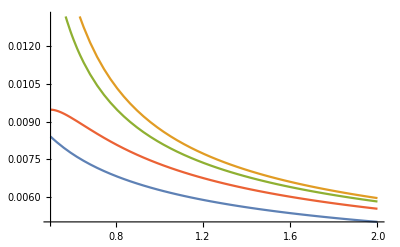

```mathematica
Plot[{αs1Loop[μ],αs2Loop[μ],αs3Loop[μ],αs[μ]},{μ,.5,2}]
```

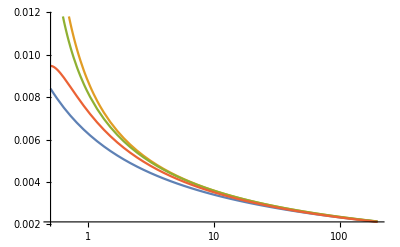

```mathematica
LogLinearPlot[{αs1Loop[μ],αs2Loop[μ],αs3Loop[μ],αs[μ]},{μ,.5,200}]
```

#### alpha tables

```mathematica
μoΛTab=1/{.19,.15,.11,.07,.046,.044,.02,.005,.001,.0006,.0005,.0003,.0001,.00003,.00001}
```

{5.26316,6.66667,9.09091,14.2857,21.7391,22.7273,50.,200.,1000.,1666.67,2000.,3333.33,10000.,33333.3,100000.}

```mathematica
nfTab=Table[0,{n,Length[μoΛTab]}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Length[nfTab]
```

15

```mathematica
ΛQCDTab=Table[ΛQCD[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD3LoopTab=Table[ΛQCD3Loop[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD2LoopTab=Table[ΛQCD2Loop[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD1LoopTab=Table[ΛQCD1Loop[nfTab[[n]]],{n,Length[nfTab]}]
```

{0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2}

{0.211473,0.211473,0.211473,0.211473,0.211473,0.211473,0.211473,0.211473,0.211473,0.211473,0.211473,0.211473,0.211473,0.211473,0.211473}

{0.231302,0.231302,0.231302,0.231302,0.231302,0.231302,0.231302,0.231302,0.231302,0.231302,0.231302,0.231302,0.231302,0.231302,0.231302}

{0.0651195,0.0651195,0.0651195,0.0651195,0.0651195,0.0651195,0.0651195,0.0651195,0.0651195,0.0651195,0.0651195,0.0651195,0.0651195,0.0651195,0.0651195}

```mathematica
μGeVTab=μoΛTab ΛQCDTab
```

{1.05263,1.33333,1.81818,2.85714,4.34783,4.54545,10.,40.,200.,333.333,400.,666.667,2000.,6666.67,20000.}

```mathematica
μGeV3LoopTab=μoΛTab ΛQCD3LoopTab
```

{1.11301,1.40982,1.92248,3.02104,4.59724,4.8062,10.5736,42.2946,211.473,352.455,422.946,704.909,2114.73,7049.09,21147.3}

```mathematica
μGeV2LoopTab=μoΛTab ΛQCD2LoopTab
```

{1.21738,1.54201,2.10274,3.30431,5.0283,5.25686,11.5651,46.2603,231.302,385.503,462.603,771.006,2313.02,7710.06,23130.2}

```mathematica
μGeV1LoopTab=μoΛTab ΛQCD1LoopTab
```

{0.342734,0.43413,0.591996,0.930279,1.41564,1.47999,3.25598,13.0239,65.1195,108.533,130.239,217.065,651.195,2170.65,6511.95}

```mathematica
α4Tab=Table[{μoΛTab[[n]],αs[μGeVTab[[n]]]},{n,Length[nfTab]}]
```

(5.26316 | 0.0071471
6.66667 | 0.00645968
9.09091 | 0.00572244
14.2857 | 0.00490186
21.7391 | 0.00432723
22.7273 | 0.00427436
50. | 0.00351701
200. | 0.00269142
1000. | 0.00212204
1666.67 | 0.00198952
2000. | 0.00194623
3333.33 | 0.00183461
10000. | 0.00163388
33333.3 | 0.00145967
100000. | 0.0013307)

```mathematica
α3Tab=Table[{μoΛTab[[n]],αs3Loop[μGeV3LoopTab[[n]]]},{n,Length[nfTab]}]
```

(5.26316 | 0.00767383
6.66667 | 0.00678239
9.09091 | 0.00591039
14.2857 | 0.00500121
21.7391 | 0.00438867
22.7273 | 0.00433302
50. | 0.00354599
200. | 0.00270307
1000. | 0.00212738
1666.67 | 0.00199385
2000. | 0.00195026
3333.33 | 0.00183794
10000. | 0.00163616
33333.3 | 0.00146126
100000. | 0.00133188)

```mathematica
α2Tab=Table[{μoΛTab[[n]],αs2Loop[μGeV2LoopTab[[n]]]},{n,Length[nfTab]}]
```

(5.26316 | 0.00766054
6.66667 | 0.00672403
9.09091 | 0.00582579
14.2857 | 0.00490941
21.7391 | 0.00430251
22.7273 | 0.00424773
50. | 0.00347779
200. | 0.0026589
1000. | 0.00209946
1666.67 | 0.00196939
2000. | 0.0019269
3333.33 | 0.00181731
10000. | 0.00162011
33333.3 | 0.00144875
100000. | 0.00132173)

```mathematica
α1Tab=Table[{μoΛTab[[n]],αs1Loop[μGeV1LoopTab[[n]]]},{n,Length[nfTab]}]
```

(5.26316 | 0.0103183
6.66667 | 0.00903262
9.09091 | 0.0077634
14.2857 | 0.00644388
21.7391 | 0.00556522
22.7273 | 0.00548603
50. | 0.00438033
200. | 0.00323423
1000. | 0.00248068
1666.67 | 0.00230987
2000. | 0.00225446
3333.33 | 0.00211249
10000. | 0.00186051
33333.3 | 0.00164542
100000. | 0.00148841)

```mathematica
<<MaTeX`
```

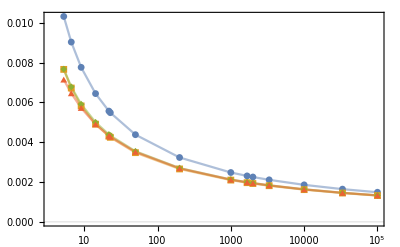

```mathematica
Show[ListLogLinearPlot[{α1Tab,α2Tab,α3Tab,α4Tab},PlotStyle->{Opacity[.5]},Joined->True],ListLogLinearPlot[{α1Tab,α2Tab,α3Tab,α4Tab},PlotMarkers->{Automatic, Small}],BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],Frame->True,Axes->False,GridLines->{{0},{0}},FrameLabel->{MaTeX["\\mu/\\Lambda_{QCD}",Magnification->1.2],MaTeX["\\alpha_s(\\mu/\\Lambda_{QCD})",Magnification->1.2]}]
```